```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yaniv/Dropbox (Cambridge University)/Mac/Documents/Stanford/bais loop bispectrum/Final_code/EFTBispectrum/Fisher produce results 3

```mathematica
(*This notebook is with neutrino mass 0.3*)
```

## Preliminaries

### Background cosmology, shift sizes and k- scales

Background Cosmology

```mathematica
lnAsback=3.044; 
nsback = 0.965; 
hback=0.673; 
ωbback = 0.02237;
ωcback = 0.1203;
mνback = 0.3;
```

```mathematica
ωmback = ωcback+ωbback+mνback/93.14;
Ωcback = ωcback/hback^2;
 Ωmback = ωmback/hback^2;
Ωbback = ωbback/hback^2;
```

Shift sizes

```mathematica
ΔlnAs = 0.1; Δh = 0.02; ΔΩm=0.04; Δωb = 0.02; Δns = 0.02; Δmν=0.25;
shifts = {ΔlnAs,Δns nsback,Δh hback,ΔΩm Ωmback,Δωb ωbback,Δmν mνback};
```

k-scales

```mathematica
kr=knl/2.8;
km=knl;
kM=knl;
```

f_NL-parameters

```mathematica
fnlfix = {fNLloc->0,fNLeq->0,fNLorth->0};
```

```mathematica
paramfix = {δc->1.68,p-> 8.52};
```

```mathematica
fnlcoefs= fnlfix[[All,1]];
```

### EFT-parameters and import best-fit

Parameters

```mathematica
biases = {b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15};
```

```mathematica
BAllcoefs = {b1,c2,b3,b4,c4,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,Bc1,Bc2,Bc3,Bc4,Be1,Be2,ce2,Bc5,Bc6,Bc7,Bc8,Bc9,Bc10,Bc11,Bc12,Bc13,Bc14,Bd1,Bd2,Bd3,Be3,Be4,Be5,Be6,Be7,Be8,Be9,Be10,Be11,Be12,Tst};
```

```mathematica
normbias =Thread[{Bb1,Bb2,Bb3,Bb4,Bb5,Bb6,Bb7,Bb8,Bb9,Bb10,Bb11,Bb12,Bb13,Bb14,Bb15}->biases];
```

```mathematica
stochp = {Bd1,Bd2,Bd3,Be1,Be2,ce2,Be3,Be4,Be5,Be6,Be7,Be8,Be9,Be10,Be11,Be12};
```

```mathematica
nonstoch = Complement[BAllcoefs,stochp];
```

Change  bestfit to new linear bias (this is an approximation, where we assume all biases rescale like the linear one)

```mathematica
changeb1[biasfix_,newb1_] := Thread[biasfix[[All,1]]->biasfix[[All,2]] newb1/biasfix[[1,2]]]
```

```mathematica
Evolve[Dgold_,Dgnew_,biasfix_]:=Join[Thread[nonstoch->(nonstoch/.biasfix)Dgold/Dgnew],Thread[stochp->(stochp/.biasfix)]]
```

Change  bestfit to new redshift

```mathematica
cfixresc[Dgold_,Dgnew_,biasfix_] := Join[Thread[stochp->(stochp/.biasfix)],Thread[biasfix[[All,1]]->biasfix[[All,2]] Dgold/Dgnew],fnlfix,paramfix]
```

```mathematica
shiftedbfix[spec_,Dg_,biasfix_]:=Table[cfixresc[Dg,spec[[5,i]],biasfix],{i,1,Length[spec[[5]]]}];
```

```mathematica
cfixrescss[Dgold_,Dgnew_,biasfix_] := Join[Thread[biasfix[[All,1]]->biasfix[[All,2]] Dgold/Dgnew],fnlfix,paramfix]
```

```mathematica
shiftedbfixss[spec_,Dg_,biasfix_]:=Table[cfixrescss[Dg,spec[[5,i]],biasfix],{i,1,Length[spec[[5]]]}];
```

Change bestfit to new redshift and no shotnoise

```mathematica
cfixrescNS[Dgold_,Dgnew_,biasfix_] := Join[{Be1->0},Thread[stochp->(stochp/.biasfix)],Thread[biasfix[[All,1]]->biasfix[[All,2]] Dgold/Dgnew],fnlfix,paramfix]//Flatten;
```

```mathematica
shiftedbfixNS[spec_,Dg_,biasfix_]:=Table[cfixrescNS[Dg,spec[[5,i]],biasfix],{i,1,Length[spec[[5]]]}];
```

Change bestfit to new redshift and no shotnoise

```mathematica
cfixrescn[Dgold_,Dgnew_,biasfix_] := Join[{Be1->n (Be1/.biasfix)},Thread[stochp->(stochp/.biasfix)],Thread[biasfix[[All,1]]->biasfix[[All,2]] Dgold/Dgnew],fnlfix,paramfix]//Flatten;
```

```mathematica
shiftedbfixn[spec_,Dg_,biasfix_]:=Table[cfixrescn[Dg,spec[[5,i]],biasfix],{i,1,Length[spec[[5]]]}];
```

### Manipulate Plin for IR-resummation and decomposition

#### IR resummation functions

```mathematica
Ho=1/2998 ;
```

```mathematica
Tcmb=2.728;
alph[ωmo_,ωbo_]:=1-0.328 Log[431 ωmo] ωbo/ωmo+0.38 Log[22.3  ωmo ](ωbo/ωmo)^2;
ss[h_,ωmo_,ωbo_]:=44.5 Log[9.83/(ωmo)]/(√(1+10(ωbo)^0.75))h;
gamma[k_,h_,ωmo_,ωbo_]:=ωmo/h  (alph[ωmo,ωbo]+(1-alph[ωmo,ωbo])/(1+(0.43 ss[h,ωmo,ωbo] k)^4));
qq[k_,h_,ωmo_,ωbo_]:= (Tcmb/2.7)^2 k/gamma[k,h,ωmo,ωbo];
L0[k_,h_,ωmo_,ωbo_]:=Log[2 ⅇ+1.8 qq[k,h,ωmo,ωbo]];
C0[k_,h_,ωmo_,ωbo_]:=14.2+731/(1+62.5 qq[k,h,ωmo,ωbo]);
Tnw[k_,h_,ωmo_,ωbo_]:=L0[k,h,ωmo,ωbo]/(L0[k,h,ωmo,ωbo]+C0[k,h,ωmo,ωbo] qq[k,h,ωmo,ωbo]^2)
```

```mathematica
Dlin[a_,h_,ωmo_]:=-a/(3 √(ωmo/h^2 (a^3 (1-ωmo/h^2)+ωmo/h^2))) (-8 ωmo/h^2 Hypergeometric2F1[-1/2,5/6,11/6,-(a^3 (1-ωmo/h^2))/(ωmo/h^2)]+(2 a^3 (1-ωmo/h^2)+5 ωmo/h^2) Hypergeometric2F1[1/2,5/6,11/6,-(a^3 (1-ωmo/h^2))/(ωmo/h^2)]);
Dlinz[z_,h_,ωmo_]:=Dlin[1/(1+z),h,ωmo];
```

```mathematica
kP[h_]:=0.05 h^-1;
PLnw[k_,z_,h_,Ωmo_,ωbo_,lnAs_,ns_]:=2 π^2 4/25 (Exp[lnAs]*10^-10 k)/(Ho^4 Ωmo^2)Dlinz[z,h,Ωmo h^2]^2(k/kP[h])^(ns-1)Tnw[k,h,Ωmo h^2,ωbo]^2;
```

```mathematica
λ=0.25;
```

```mathematica
pwnwdat[dat_,z_,h_,Ωmo_,ωbo_,lnAs_,ns_]:=Module[{plindat,iplin,klin,plinEHtab,iR,fk,pnw,pw,ipnw,ipw,Σ2,δΣ2},
plindat=dat;
klin=plindat⟦All,1⟧;
plinEHtab = Table[{klin[[i]],PLnw[klin[[i]],z,h,Ωmo,ωbo,lnAs,ns]},{i,1,Length[klin]}];
iR=Interpolation[Transpose@{klin,plindat⟦All,2⟧/plinEHtab⟦All,2⟧}];
fk[k_]:=NIntegrate[iR[10^x] PDF[NormalDistribution[Log10[k],λ]][x],{x,Log10[k]-4 λ,Log10[k]+4 λ},Method->{"LocalAdaptive","SymbolicProcessing"->0}];
pnw=Table[{klin⟦i⟧,plinEHtab⟦i,2⟧ fk[klin⟦i⟧]},{i,1,Length[klin]}];
pw=Table[{klin⟦i⟧,plindat⟦i,2⟧-pnw⟦i,2⟧},{i,1,Length[klin]}];
ipnw=Interpolation[pnw];
ipw=Interpolation[pw];
Σ2=1/(6 π^2)NIntegrate[(1-SphericalBesselJ[0,q losc]+2 SphericalBesselJ[2,q losc])ipnw[q]/.losc->110,{q,klin⟦1⟧,0.2}];
δΣ2=1/(2 π^2)NIntegrate[SphericalBesselJ[2,q losc]ipnw[q]/.losc->110,{q,klin⟦1⟧,0.2}];
{pnw,pw,Σ2,δΣ2}
]
```

```mathematica
pwnwavg[dat_,f_,z_,h_,Ωmo_,ωbo_,lnAs_,ns_]:=Module[{full,klin,plindat,pnw,pw,ipnw,ipw,Σ2,δΣ2,Σtot2avg},
full  = pwnwdat[dat,z,h,Ωmo,ωbo,lnAs,ns];
plindat=dat;
klin=plindat⟦All,1⟧;
pnw = full[[1]];
pw= full[[2]];
Σ2= full[[3]];
δΣ2= full[[4]];
Σtot2avg = -1/15 f^2 (2 δΣ2-5 Σ2)+Σ2+(2 f Σ2)/3;

Table[{klin[[i]],pnw[[i,2]]+ Exp[-klin[[i]]^2 Σtot2avg]pw[[i,2]]},{i,1,Length[klin]}]]
pwnwavgTree[dat_,f_,z_,h_,Ωmo_,ωbo_,lnAs_,ns_]:=Module[{full,klin,plindat,pnw,pw,ipnw,ipw,Σ2,δΣ2,Σtot2avg},
full  = pwnwdat[dat,z,h,Ωmo,ωbo,lnAs,ns];
plindat=dat;
klin=plindat⟦All,1⟧;
pnw = full[[1]];
pw= full[[2]];
Σ2= full[[3]];
δΣ2= full[[4]];
Σtot2avg = -1/15 f^2 (2 δΣ2-5 Σ2)+Σ2+(2 f Σ2)/3;
Table[{klin[[i]],pnw[[i,2]]+(1+klin[[i]]^2 Σtot2avg) Exp[-klin[[i]]^2 Σtot2avg]pw[[i,2]]},{i,1,Length[klin]}]]
```

```mathematica
IRrep[res_] := {Pnw->( res[[1]]//Interpolation),Pw-> (res[[2]]//Interpolation),Σ2-> res[[3]],δΣ2-> res[[4]]}
```

```mathematica
Σtot2[μ_,f_]:=(1+f μ^2(2+f))Σ2+f^2 μ^2(μ^2-1)δΣ2
```

#### Plin decomposition

```mathematica
kmax=1000;
```

```mathematica
highval[plindat_]:=Module[{nshigh,Ashigh,pextrahigh},
nshigh =(( Log[plindat[[-1]]]-Log[plindat[[-2]]])[[2]])/(( Log[plindat[[-1]]]-Log[plindat[[-2]]])[[1]]);
Ashigh = (plindat[[-1]][[2]])/(plindat[[-1]][[1]])^nshigh;

pextrahigh = Table[{Log10[plindat[[-1]][[1]]]/0.01+0.01+10^((i-1) 0.01), Ashigh ((Log10[plindat[[-1]][[1]]]/0.01+0.01+10^((i-1) 0.01))/(plindat[[-1]][[1]]))^nshigh},{i,1,IntegerPart[Log10[kmax]/0.01]+1}];
Join[plindat,pextrahigh]
]
```

```mathematica
(* Nmax log k bins, form kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
kmaxFit = 0.6;
kminFit = 0.001;
```

```mathematica
genPlinCoef[imax_,dat_]:=Module[{knFit,k,MyPsmoothtab,errors,Parameters,MyFitFunctions,nlm,Plin,Pinteger,coefnowig},
Plin=Interpolation[dat];
knFit=kBins[100,kminFit,kmaxFit];
MyPsmoothtab = Table[{knFit⟦i⟧,Plin[knFit⟦i⟧]},{i,1,Length[knFit]}];
errors=Flatten[Table[{MyPsmoothtab⟦i,2⟧ 10^-6},{i,1,Length[knFit]}]];
kuv1=0.069;
kuv2=0.0082;
kuv3=0.0013;
kuv4=0.0000135;
kuv5 =0.01;
kpeak1=-0.034;
kpeak2=-0.001;
kpeak3=-0.000076;
kpeak4=-0.0000156;

Parameters=Flatten[Table[{a1[i],a2[i],a3[i],a4[i]},{i,0,imax}]];
MyFitFunctions=Delete[Flatten[Join[{1/(1+k^2/kuv5^2)},Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]]],2];
nlm=LinearModelFit[MyPsmoothtab,MyFitFunctions,k,Weights->1/errors^2,IncludeConstantBasis->False]; 
Pinteger[k_]=nlm[k];
coefnowig=N[nlm["BestFitParameters"],50];
{Pinteger[q],coefnowig}]
```

```mathematica
MyFitFunctions=Delete[Flatten[Join[{1/(1+k^2/kuv5^2)},Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,3}]]],2];
```

#### Final needed functions

```mathematica
IRls[dat_,hfactor_,Ωmfacor_,ωbfacor_,Asfactor_,nsfactor_,zpk_,f1_]:=Module[{iplin,splitwnw,ls,lsnw,iplinnw,iplinw,sig,iplinresum,iplinresumTree},
iplin =highval[dat]//Interpolation;
splitwnw=pwnwdat[dat,zpk,hback*hfactor,Ωmback*Ωmfacor,ωbback*ωbfacor,lnAsback+Asfactor,nsback*nsfactor];
ls=genPlinCoef[3,dat][[2]];
lsnw=genPlinCoef[3,splitwnw[[1]]][[2]];
iplinnw = highval[splitwnw[[1]]]//Interpolation;
iplinw = highval[splitwnw[[2]]]//Interpolation;
sig=Σtot2[μ,f1]/.IRrep[splitwnw];
iplinresum = pwnwavg[dat,f1,zpk,hback*hfactor,Ωmback*Ωmfacor,ωbback*ωbfacor,lnAsback+Asfactor,nsback*nsfactor]//Interpolation; 
iplinresumTree = pwnwavgTree[dat,f1,zpk,hback*hfactor,Ωmback*Ωmfacor,ωbback*ωbfacor,lnAsback+Asfactor,nsback*nsfactor]//Interpolation; 
{ls,lsnw,iplin,iplinnw,iplinw,sig,iplinresum,iplinresumTree,f1}
]
```

```mathematica
Plinsubs[survey_,zpk_]:=Module[{fback,fΩmhigh,fΩmlow,fωbhigh,fωblow,fhhigh,fhlow,fmνhigh,fmνlow,path},
path = ToString[survey];
{fback,fΩmhigh,fΩmlow,fωbhigh,fωblow,fhhigh,fhlow,fmνhigh,fmνlow}=Import["plins/"<>path<>"/allfs.dat"]//Flatten;
{IRls[Import["plins/"<>path<>"/pk_fid.dat"],1,1,1,0,1,zpk,fback],
IRls[Import["plins/"<>path<>"/pk_lnAs_pl.dat"],1,1,1,ΔlnAs ,1,zpk,fback],
IRls[Import["plins/"<>path<>"/pk_lnAs_min.dat"],1,1,1,-ΔlnAs ,1,zpk,fback],
IRls[Import["plins/"<>path<>"/pk_ns_pl.dat"],1,1,1,0,1+Δns,zpk,fback],
IRls[Import["plins/"<>path<>"/pk_ns_min.dat"],1,1,1,0,1-Δns,zpk,fback],
IRls[Import["plins/"<>path<>"/pk_h_pl.dat"],1+Δh,1,1,0,1,zpk,fhhigh],
IRls[Import["plins/"<>path<>"/pk_h_min.dat"],1-Δh,1,1,0,1,zpk,fhlow],
IRls[Import["plins/"<>path<>"/pk_Om_pl.dat"],1,1+ΔΩm,1,0,1,zpk,fΩmhigh],
IRls[Import["plins/"<>path<>"/pk_Om_min.dat"],1,1-ΔΩm,1,0,1,zpk,fΩmlow],
IRls[Import["plins/"<>path<>"/pk_ob_pl.dat"],1,1,1+Δωb,0,1,zpk,fωbhigh],
IRls[Import["plins/"<>path<>"/pk_ob_min.dat"],1,1,1-Δωb,0,1,zpk,fωblow],
IRls[Import["plins/"<>path<>"/pk_nu_pl.dat"],1,1,1,0,1,zpk,fmνhigh],
IRls[Import["plins/"<>path<>"/pk_nu_min.dat"],1,1,1,0,1,zpk,fmνlow]}]
```

```mathematica
GetT[path_]:={Interpolation[Import["plins/"<>path<>"/Tk_fid.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_lnAs_pl.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_lnAs_min.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_ns_pl.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_ns_min.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_h_pl.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_h_min.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_Om_pl.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_Om_min.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_ob_pl.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_ob_min.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_nu_pl.dat"]],
Interpolation[Import["plins/"<>path<>"/Tk_nu_min.dat"]]};
```

```mathematica
PlinsubsT[survey_,zpk_]:=Module[{Ts,Pks},
Pks = Plinsubs[survey,zpk];
Ts = GetT[ToString[survey]];
Table[Join[Pks[[i]],{Ts[[i]]}],{i,1,Length[Ts]}]]
```

### Useful functions

Number format for jmat imports

```mathematica
fi[a_]:=NumberForm[a,{5,5}]
Tfi[a_]:=ToString[fi[a]]
```

Quick evalutations

```mathematica
EV[f_,tab_]:=Monitor[Table[f[tab[[s]]],{s,1,Length[tab]}],s];
EV2[f_,tab_]:=Monitor[Table[f[tab[[s,1]],tab[[s,2]],tab[[s,3]]],{s,1,Length[tab]}],s];
```

Some Matrix Manipulation

```mathematica
Upperrightpre[mat_]:=Table[Table[mat[[i,j]],{i,1,j}],{j,1,Length[mat]}];
```

```mathematica
Upperright[mat_]:=Transpose[Table[PadRight[Upperrightpre[mat][[i]],Length[mat]],{i,1,Length[mat]}]]
```

```mathematica
Mirror[mat_]:=Transpose[mat-DiagonalMatrix[Diagonal[mat]]]+mat;
```

```mathematica
RemoveRowCol[A_,n_]:=Delete[Transpose[Delete[Transpose[A], n]],n]
```

```mathematica
RemoveRowCol2[A_,list_]:=Module[{listor,A2},
listor = Reverse[Sort[list]];
A2=A;
For[i=1,i<Length[list]+1,i++,A2=RemoveRowCol[A2,listor[[i]]]];
A2]
```

Get triangles and keff

```mathematica
makeTri[kmin_,kmax_,dk_]:=Module[{kpairs,kpairstriangle,Alltriangs,ktab},
ktab = Table[kmin+i*dk,{i,0,Floor[(kmax-kmin)/dk]}];
kpairs = Flatten[Table[Table[Table[{ktab[[i]],ktab[[j]],ktab[[k]]},{i,1,j}],{j,1,k}],{k,1,Length[ktab]}],2];
kpairstriangle =Monitor[Table[If[kpairs⟦i,1⟧<kpairs⟦i,3⟧-kpairs⟦i,2⟧,0,kpairs[[i]]],{i,1,Length[kpairs]}],i]//DeleteDuplicates;
Alltriangs=DeleteCases[kpairstriangle,0];
Table[Alltriangs[[i]],{i,1,Length[Alltriangs]}]//N;
Table[Alltriangs[[i]],{i,1,Length[Alltriangs]}]//Sort
];
```

```mathematica
Getkeff[{k1_,k2_,k3_},Δk_]:=Module[{k1eff,k2eff,k3eff,VT},

VT =NIntegrate[q1 q2 q3 Boole[q1<=q2+q3]Boole[q2<=q1+q3]Boole[q3<=q1+q2],{q1,k1-Δk/2,k1+Δk/2},{q2,k2-Δk/2,k2+Δk/2},{q3,k3-Δk/2,k3+Δk/2}];
k1eff = 1/VT NIntegrate[q1 q2 q3 Min[{q1,q2,q3}] Boole[q1<=q2+q3]Boole[q2<=q1+q3]Boole[q3<=q1+q2],{q1,k1-Δk/2,k1+Δk/2},{q2,k2-Δk/2,k2+Δk/2},{q3,k3-Δk/2,k3+Δk/2}];
k2eff =1/VT NIntegrate[q1 q2 q3 (q1 q2 q3)/(Min[{q1,q2,q3}]Max[{q1,q2,q3}]) Boole[q1<=q2+q3]Boole[q2<=q1+q3]Boole[q3<=q1+q2],{q1,k1-Δk/2,k1+Δk/2},{q2,k2-Δk/2,k2+Δk/2},{q3,k3-Δk/2,k3+Δk/2}];
k3eff = 1/VT NIntegrate[q1 q2 q3 Max[{q1,q2,q3}] Boole[q1<=q2+q3]Boole[q2<=q1+q3]Boole[q3<=q1+q2],{q1,k1-Δk/2,k1+Δk/2},{q2,k2-Δk/2,k2+Δk/2},{q3,k3-Δk/2,k3+Δk/2}];
{k1eff,k2eff,k3eff}

]
```

```mathematica
makeTrikeff[kmin_,kmax_,dk_]:=Module[{tris},
tris=makeTri[kmin,kmax,dk];
Monitor[Table[Getkeff[tris[[i]],dk],{i,1,Length[tris]}],(i*100.0)/Length[tris]]
]
```

Get Powerspectrum multipoles

```mathematica
mono[f_]:=(f//Expand)/.μ^(n_.)-> (1+(-1)^n)/(2 (1+n))
quad[f_]:=(f-(f/.μ-> 0)//Expand)/.μ^(n_.)-> (5 (1+(-1)^n) n)/(2 (1+n) (3+n))
```

Make list of derivatives, the order is  lnAs, ns h, Ωm, ωb, log(νm), log(b1), BAllcoefs[[2;;]]}

```mathematica
Makederiv[prederiv_]:=Module[{EFTderiv,cosmoderiv,derivs,fnlderiv},
EFTderiv=Table[D[prederiv[[1]],BAllcoefs[[i]]],{i,1,Length[BAllcoefs]}];
EFTderiv[[1]]=EFTderiv[[1]]b1;
cosmoderiv = (prederiv[[2;; ;;2]]-prederiv[[3;; ;;2]])/(2 shifts);
cosmoderiv[[6]]=mνback cosmoderiv[[6]];

fnlderiv=Table[D[prederiv[[1]],fnlcoefs[[i]]],{i,1,Length[fnlcoefs]}];
derivs= Join[cosmoderiv,fnlderiv,EFTderiv];
derivs
]
```

Combine matrices for 4 sky correlations

```mathematica
cosmopars ={lnAs,ns,h,Ωm,ωb,mν};
```

```mathematica
cosmopar= Length[cosmopars]+Length[fnlcoefs];
```

```mathematica
CombineMs[Ms_]:=Module[{MAu,MBu,double,l,Msu},
l = Length[Ms];
Msu = Table[Upperright[Ms[[i]]],{i,1,Length[Ms]}];
double = Table[Table[0,{i,1,cosmopar+l(Length[Msu[[1]]]-cosmopar)}],{j,1,cosmopar+l(Length[Msu[[1]]]-cosmopar)}];
For[i=1,i<cosmopar+1,i++,
For[j=1,j<cosmopar+1,j++,
double[[i,j]]=Sum[Msu[[s,i,j]],{s,1,l}];]];
For[i=1,i<cosmopar+1,i++,
For[j=cosmopar+1,j<Length[double],j+=l,
For[s=0,s<l,s++,
double[[i,j+s]]=Msu[[s+1,i,(j-(cosmopar+1))/l+(cosmopar+1)]];]]];
For[i=cosmopar+1,i<Length[double],i+=l,
For[j=cosmopar+1,j<Length[double],j+=l,
For[s=0,s<l,s++,
double[[i+s,j+s]]=Msu[[s+1,(i-(cosmopar+1))/l+cosmopar+1,(j-(cosmopar+1))/l+cosmopar+1]];]
]];
Mirror[double]
]
```

Some Fisher matrix  manipulations (comeback)

```mathematica
AllParams =Join[ cosmopars,fnlcoefs,BAllcoefs];
```

```mathematica
Getpos[arr_]:=Table[Position[AllParams,arr[[i]]],{i,1,Length[arr]}]//Flatten;
```

```mathematica
SubFisher[Fisher_,params_]:=Fisher[[Getpos[params],Getpos[params]]];
```

```mathematica
BAllcoefs4sky = Join[{BAllcoefs},{BAllcoefs},{BAllcoefs},{BAllcoefs}]//Transpose//Flatten;
AllParams4sky =Join[ cosmopars,fnlcoefs,BAllcoefs4sky];
```

```mathematica
Getpos4sky[arr_]:=Table[Position[AllParams4sky,arr[[i]]],{i,1,Length[arr]}]//Flatten;
```

```mathematica
SubFisher4sky[Fisher_,params_]:=Fisher[[Getpos4sky[params],Getpos4sky[params]]];
```

```mathematica
GetError[F_]:=Quiet[(Diagonal[Inverse[F]])^(1/2)]
```

```mathematica
Getzeffs[spec_,cut_]:={Total[spec[[1,;;cut]]spec[[4,;;cut]]]/Total[spec[[4,;;cut]]],Total[spec[[1,cut+1;;]]spec[[4,cut+1;;]]]/Total[spec[[4,cut+1;;]]]}
```

```mathematica
fixsurv[spec_,dkk_] := Table[{dk->dkk[[2]],nb->spec[[2,i]],Vs->spec[[3,i]]},{i,1,Length[spec[[1]]]}];
```

```mathematica
Getnbeff[spec_,cut_]:={Total[spec[[2,;;cut]]spec[[4,;;cut]]]/Total[spec[[4,;;cut]]],Total[spec[[2,cut+1;;]]spec[[4,cut+1;;]]]/Total[spec[[4,cut+1;;]]]}
```

```mathematica
getkf[spec_]:=2π/spec[[3]]^(1/3)
getkfeff[spec_,cut_]:={Total[getkf[spec][[;;cut]]spec[[4,;;cut]]]/Total[spec[[4,;;cut]]],Total[getkf[spec][[cut+1;;]]spec[[4,cut+1;;]]]/Total[spec[[4,cut+1;;]]]}
```

Find neighbours for linear interpolation

```mathematica
TriangMemb[tri_,bin_]:={MemberQ[bin,tri[[1]]],MemberQ[bin,tri[[2]]],MemberQ[bin,tri[[3]]]}
Tflist[tri_,bin_] :=bin TriangMemb[tri]/.True->0/.False->1
Isflat[tri_]:=Round[10^3 tri[[1]]]+Round[10^3 tri[[2]]]==Round[10^3 tri[[3]]]
```

```mathematica
Neighbourpos[smalltri_,tri_,bin_]:=If[MemberQ[smalltri,tri],{Position[smalltri,tri],Position[smalltri,tri]},If[Isflat[tri]&&(!MemberQ[smalltri,tri+Tflist[tri,bin]]||!MemberQ[smalltri,tri-Tflist[tri,bin]]),{Position[Round[10^3smalltri],Round[10^3(tri-{bin,bin,2bin})]],Position[Round[10^3smalltri],Round[10^3(tri+{bin,bin,2bin})]]},{Position[Round[10^3smalltri],Round[10^3(tri-Tflist[tri,bin])]],Position[Round[10^3smalltri],Round[10^3(tri+Tflist[tri,bin])]]}]]//Flatten
```

```mathematica
disttab[tri_, Base_]:=Table[(Abs[tri-Base[[i]]]^2)//Total,{i,1,Length[Base]}];
Getposmin[tri_, Base_] := Position[Round[10^5 disttab[tri,Base]],Round[10^5(disttab[tri,Base]//Sort)[[1]]]]//Flatten
Getminposlist[fine_,coarse_]:=Monitor[Table[Getposmin[fine[[j]], coarse],{j,1,Length[fine]}],j]
```

```mathematica
Producefine[func_,finecoarse_]:=Monitor[Table[func[[finecoarse[[i]]]]/Length[finecoarse[[i]]]//Total,{i,1,Length[finecoarse]}],i]
```

### Priors including 4sky

We put a BBN prior on ωb, Gaussian priors of width 2 or 4 on all biases except b1, where we put a log prior. Also we put a carefully engineered prior of width 1 on log  neutrino masses which mimics a flat prior form 0.06 to 0.9 on neutrinos (as previously done in arxiv 1909.07951)

```mathematica
σωb=0.000036;
```

```mathematica
priorspre={1/ϵ,1/ϵ,1/ϵ,1/ϵ,σωb,1,1/ϵ,1/ϵ,1/ϵ,(*1/ϵ*)√0.8,(*1/ϵ*)2,2,(*2*)2,(*1/ϵ*)(*2*)2,2,2,2,2,2,2,2,2,2,2,4,4,4,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2};
Priors=DiagonalMatrix[1/priorspre^2/. ϵ->0];
```

Create a correlated 4 sky prior

```mathematica
blockArray[mat_]:=SparseArray[Tuples[Range@#-{1,0,0}].{Rest@#,{1,0},{0,1}}&@Dimensions@mat->Flatten@mat]
```

```mathematica
ρ12 = (1-0.1^2/2);
ρ13 =( 1-0.2^2/2);
```

```mathematica
corrmat={{1, ρ12, ρ13,ρ12 ρ13},
		{ρ12,1, ρ12 ρ13, ρ13},
		{ρ13, ρ12 ρ13, 1, ρ12},
		{ρ12 ρ13, ρ13, ρ12, 1}};
```

```mathematica
buildCorrPrior[priorlist_, cosmolen_]:=Module[{fullPriorpre,fullPrior},
fullPriorpre=blockArray[Table[(priorlist//Diagonal)[[ i]]Inverse[corrmat],{i,cosmolen+1, Length[priorlist]}]];
fullPrior=ArrayPad[fullPriorpre,{{cosmolen,0},{cosmolen,0}}]//Normal;
fullPrior[[5,5]]=1/σωb^2;
fullPrior[[6,6]]=1;
fullPrior]
```

```mathematica
Prior4sky = buildCorrPrior[Priors,9];
```

## Powespectrum Fisher

### Perliminary functions and definitions

Counter term definition

```mathematica
CounterP13=(b1+f1 μ^2)plin[k](-(Bc1 k^2)/km^2+(f1 (Bc2-(Bc4 f1)/2) k^2 μ^2)/kr^2-(Bc3 f1^2 k^2 μ^4)/(2 kr^2));
StochasticP22=1/nb(Be1+(Be2 k^2)/km^2+(3 ce2 k^2 μ^2)/(2 km^2));
```

```mathematica
PCounter[k_,plin_,f1_]=2CounterP13+StochasticP22;
```

Loop definitions and imports

```mathematica
DumpGet["tabs/P13interp.mx"]; DumpGet["tabs/P22interp.mx"];
```

```mathematica
P13coefs[f1_] = Import["tabs/P13simpcoefs.m"]; P13kers[k_] = Import["tabs/P13simppermks.m"];
```

```mathematica
P22coefs[f1_] = Import["tabs/P22simpcoefs.m"]/.b2->(c2 + c4)/(√2)/.b5->(c2 - c4)/(√2); P22kers[k_] = Import["tabs/P22simppermks.m"];
```

```mathematica
P13n[k_]:=P13kers[k].P13interp[k];
P22n[k_]:=P22kers[k].P22interp[k];
```

```mathematica
P13ev[P13_,ls_,f_,Plink_] := P13.ls.P13coefs[f] Plink;
P22ev[P22_,ls_,f_] := P22.ls.ls.P22coefs[f] ;
```

f_NL definitions

```mathematica
PNG[k_,{fnl_,βs_},{plin_,f1_,Tα_}]:=(4 (-1+b1) fnl (k/knl)^βs δc (b1+f1 μ^2) plin[k])/Tα[k]
```

```mathematica
PNGfull[k_,{plin_,f1_,Tα_}]:=PNG[k, {fNLloc,0},{plin,f1,Tα}]+PNG[k,{fNLeq,2},{plin,f1,Tα}]+PNG[k,{fNLorth,2},{plin,f1,Tα}]
```

### Derivatives Resummed

Tree derivatives

```mathematica
PTreeDerivs[k_,pks_]:=Module[{PTreeresum,prederiv,EFTderiv,cosmoderiv,derivs},
PTreeresum[arr_]:=(b1+arr[[4]] μ^2)^2(arr[[1]][k]+(1+k^2 arr[[3]])Exp[-k^2 arr[[3]]]arr[[2]][k]);
prederiv = Table[PTreeresum[pks[[i]][[{4,5,6,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Counter derivatives

```mathematica
PCounterDerivs[k_,pks_]:=Module[{Pcounteresum,prederiv,EFTderiv,cosmoderiv,derivs},
Pcounteresum[arr_]:=PCounter[k,arr[[2]],arr[[4]]](1-Exp[-k^2 arr[[3]]])+Exp[-k^2 arr[[3]]]PCounter[k,arr[[1]],arr[[4]]];
prederiv = Table[Pcounteresum[pks[[i]][[{3,4,6,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Loop derivatives

```mathematica
PLoopDerivs[k_,pks_]:=Module[{P13,P22,Plint,Ploopeval,Ploopresum,PTreeresum,prederiv,EFTderiv,cosmoderiv,derivs},
P13=P13n[k]; P22=P22n[k]; Plint[Plin_]=Plin[k];
Ploopeval[ls_,plin_,f_]:= P13ev[P13,ls,f,Plint[plin]]+ P22ev[P22,ls,f];
Ploopresum[arr_]:=Ploopeval[arr[[4]],arr[[2]],arr[[6]]](  1- Exp[-k^2 arr[[5]]])+Exp[-k^2 arr[[5]]]Ploopeval[arr[[3]],arr[[1]],arr[[6]]];
prederiv = Table[Ploopresum[pks[[i]][[{3,4,1,2,6,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]];
```

f_NL derivatives

```mathematica
PNGDerivs[k_,pks_]:=Module[{PTreeresum,prederiv,EFTderiv,cosmoderiv,derivs},
prederiv = Table[PNGfull[k,pks[[i]][[{3,9,10}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Full P1loop derivatives

```mathematica
P1Loopderivs[k_,pks_]:=Series[PLoopDerivs[k,pks]+PTreeDerivs[k,pks]+PCounterDerivs[k,pks]+PNGDerivs[k,pks],{μ,0,10}]//Normal;
```

### Derivatives not-Resummed

Tree derivatives

```mathematica
PTreeDerivsNR[k_,pks_]:=Module[{PTreeresum,prederiv,EFTderiv,cosmoderiv,derivs},
PTreeresum[arr_]:=(b1+arr[[2]] μ^2)^2 arr[[1]][k];
prederiv = Table[PTreeresum[pks[[i]][[{3,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Counter derivatives

```mathematica
PCounterDerivsNR[k_,pks_]:=Module[{Pcounteresum,prederiv,EFTderiv,cosmoderiv,derivs},
Pcounteresum[arr_]:=PCounter[k,arr[[1]],arr[[2]]];
prederiv = Table[Pcounteresum[pks[[i]][[{3,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Loop derivatives

```mathematica
PLoopDerivsNR[k_,pks_]:=Module[{P13,P22,Plint,Ploopeval,Ploop,prederiv,EFTderiv,cosmoderiv,derivs},
P13=P13n[k]; P22=P22n[k]; Plint[Plin_]=Plin[k];
Ploopeval[ls_,plin_,f_]:= P13ev[P13,ls,f,Plint[plin]]+ P22ev[P22,ls,f];
Ploop[arr_]:=Ploopeval[arr[[1]],arr[[2]],arr[[3]]];
prederiv = Table[Ploop[pks[[i]][[{1,3,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]];
```

f_NL derivatives

```mathematica
PNGDerivs[k_,pks_]:=Module[{PTreeresum,prederiv,EFTderiv,cosmoderiv,derivs},
prederiv = Table[PNGfull[k,pks[[i]][[{3,9,10}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Full P1loop derivatives

```mathematica
P1LoopderivsNR[k_,pks_]:=Series[PLoopDerivsNR[k,pks]+PTreeDerivsNR[k,pks]+PCounterDerivsNR[k,pks]+PNGDerivs[k,pks],{μ,0,10}]//Normal;
```

### Covariance

Fisher with Analytical covariance

```mathematica
PTree[k_,plin_,f1_]:=(b1+f1 μ^2)^2 plin[k]+Be1/nb;
```

```mathematica
CovP[k_,pks_,bias_]:=( (4 π^2)/(k^2 dk Vs))^-1(Series[1/(PTree[k,pks[[1,3]],pks[[1,9]]]/.bias),{μ,0,30}]//Normal)^2;
```

```mathematica
CovP2[k_,pks_,bias_,Survey_,f1_]:=( (4 π^2)/(k^2 dk Vs))^-1(Series[1/(PTree[k,pks[[1,3]],f1]/.bias),{μ,0,30}]//Normal)^2/.Survey;
```

```mathematica
CovPmulti[k_,pks_,bias_,Survey_,fs_]:=Monitor[Sum[CovP2[k,pks,bias[[i]],Survey[[i]],fs[[i]]],{i,1,Length[bias]}],i]
```

```mathematica
GetFullzCovP[ks_,pks_,spec_,Dg_,biasfix_,dkk_]:=CovPmulti[ks,pks,shiftedbfix[spec,Dg,biasfix],fixsurv[spec,dkk],spec[[-1]]]//Expand;
```

```mathematica
GetFullzCovPNS[ks_,pks_,spec_,Dg_,biasfix_,dkk_]:=CovPmulti[ks,pks,shiftedbfixNS[spec,Dg,biasfix],fixsurv[spec,dkk],spec[[-1]]]//Expand;
```

```mathematica
GetFullzCovPn[ks_,pks_,spec_,Dg_,biasfix_,dkk_]:=CovPmulti[ks,pks,shiftedbfixn[spec,Dg,biasfix],fixsurv[spec,dkk],spec[[-1]]]//Expand;
```

### FisherMatrix

Fisher with Numerical covariance

```mathematica
GetFisherPNum[ktab_,biasfix_,pks_,Survey_,Covnum_]:=Module[{hartlapedcov,derivs,monoquad},
derivs = Table[P1Loopderivs[ktab[[i]],pks],{i,1,Length[ktab]}]/.biasfix/.Survey;
monoquad = Join[mono[derivs],quad[derivs]];
(2048 - Length[Covnum] - 2)/(2048 - 1)*(monoquad//Transpose).Inverse[Covnum].monoquad]
```

Fisher with Numerical covariance - Non-Resummed

```mathematica
GetFisherPNumNR[ktab_,biasfix_,pks_,Survey_,Covnum_]:=Module[{hartlapedcov,derivs,monoquad},
derivs = Table[P1LoopderivsNR[ktab[[i]],pks],{i,1,Length[ktab]}]/.biasfix/.Survey;
monoquad = Join[mono[derivs],quad[derivs]];
(2048 - Length[Covnum] - 2)/(2048 - 1)*(monoquad//Transpose).Inverse[Covnum].monoquad]
```

Fisher with Analytical covariance monopole and quadrupole

```mathematica
removelg2[a_]:=(a//mono)+(a//quad)LegendreP[2,μ]
```

```mathematica
GetFisherP02[ktab_,biasfix_,pks_,Survey_]:=Module[{derivred,derivs,cov,Fpre,ktabnew},
derivs = removelg2[Table[P1Loopderivs[ktab[[i]],pks],{i,1,Length[ktab]}]/.biasfix/.Survey];
cov = Table[CovP[ktab[[i]],pks,biasfix],{i,1,Length[ktab]}]/.Survey;
Fpre =Monitor[Sum[(KroneckerProduct[derivs[[i]],derivs[[i]]])cov[[i]],{i,1,Length[derivs]}],i];
Mirror[mono[Upperright[Fpre]]]]
```

Fisher with Analytical covariance monopole and quadrupole no shotnoise

```mathematica
GetFisherP02nos[ktab_,biasfix_,biasfixcov_,pks_,Survey_]:=Module[{derivred,derivs,cov,Fpre,ktabnew},
derivs = removelg2[Table[P1Loopderivs[ktab[[i]],pks],{i,1,Length[ktab]}]/.biasfix/.Survey];
cov = Table[CovP[ktab[[i]],pks,biasfixcov],{i,1,Length[ktab]}]/.Survey;
Fpre =Monitor[Sum[(KroneckerProduct[derivs[[i]],derivs[[i]]])cov[[i]],{i,1,Length[derivs]}],i];
Mirror[mono[Upperright[Fpre]]]]
```

Fisher with Analytical covariance

```mathematica
GetFisherP[ktab_,biasfix_,pks_,Survey_]:=Module[{derivred,derivs,cov,Fpre,ktabnew},
derivs = Table[P1Loopderivs[ktab[[i]],pks],{i,1,Length[ktab]}]/.biasfix/.Survey;
cov = Table[CovP[ktab[[i]],pks,biasfix],{i,1,Length[ktab]}]/.Survey;
Fpre =Monitor[Sum[(KroneckerProduct[derivs[[i]],derivs[[i]]])cov[[i]],{i,1,Length[derivs]}],i];
Mirror[mono[Upperright[Fpre]]]]
```

Get Fisher List

```mathematica
GetFisherPnew[derivs_,covs_] := Mirror[mono[Upperright[Monitor[Sum[(KroneckerProduct[derivs[[i]],derivs[[i]]])covs[[i]],{i,1,Length[derivs]}],i]]]];
```

```mathematica
GetFisherPnewNum[derivs_,covs_] := (2048 - Length[covs] - 2)/(2048 - 1)*(derivs//Transpose).Inverse[covs].derivs
```

```mathematica
GetFisherlistP[derivs_, covs_]:=Monitor[Table[Mirror[mono[Upperright[(KroneckerProduct[derivs[[i]],derivs[[i]]])covs[[i]]]]],{i,1,Length[derivs]}],i];
```

## Bispectrum Fisher

### Imports and potential exports

Some path functions

```mathematica
ExportKer[file_,func_,triang_]:=If[FileExistsQ[file],x=x,Export[file,func[triang]]];
savelpath[triang_,diag_]:="saveloops/"<>ToString[diag]<>"/"<>Tfi[triang[[1]]]<>"_"<>Tfi[triang[[2]]]<>"_"<>Tfi[triang[[3]]]<>"_.m";
jmatimp[triang_,diag_]:=Import["newbasiscreatejmats/jmats/"<>ToString[diag]<>"/"<>Tfi[triang[[1]]]<>"_"<>Tfi[triang[[2]]]<>"_"<>Tfi[triang[[3]]]<>"_.h5","jmat"];
```

Import kernels

```mathematica
B222kers[{k1_,k2_,k3_}] = Transpose[Import["tabs/B222simppermks.m"]];
B3211kers[{k1_,k2_,k3_}] = TensorTranspose[Import["tabs/B3211simppermks.m"],{3,1,2}];
B3212kers[{k1_,k2_,k3_}] = TensorTranspose[Import["tabs/B3212simppermks.m"],{3,1,2}];
B411kers[{k1_,k2_,k3_}] = TensorTranspose[Import["tabs/B411simppermks.m"],{3,1,2}];
```

Export evaluated things

```mathematica
Tabexport[triangs_]:=Module[{B222precomp,file1,file2,file3,file4},
Monitor[
For[i=1,i<Length[triangs]+1,i++,
ExportKer[savelpath[triangs[[i]],B222],B222kers,triangs[[i]]];
ExportKer[savelpath[triangs[[i]],B3211],B3211kers,triangs[[i]]];
ExportKer[savelpath[triangs[[i]],B3212],B3212kers,triangs[[i]]];
ExportKer[savelpath[triangs[[i]],B411],B411kers,triangs[[i]]]];
,i]]
```

### Preliminary functions and definitions

Angle definitions

```mathematica
ys[k1_,k2_,k3_]=(-k1^2-k2^2+k3^2)/(2 k1 k2); y13s[k1_,k2_,k3_]=(-k1^2+k2^2-k3^2)/(2 k1 k3);
```

Tree term definition

```mathematica
BTree[k1_,k2_,k3_,Plin_,f1_,y_,y13_]=
Import["tabs/Treelist.m"]/.normbias/.b2-> (c2 + c4)/(√2)/.b5-> (c2 - c4)/(√2);
```

Counter term definition

```mathematica
counterlist2=Import["tabs/counterlistG.m"]/.b2-> (c2 + c4)/(√2)/.b5-> (c2 - c4)/(√2);
```

```mathematica
BCounter[k1_,k2_,k3_,Plin_,f1_,y_,y13_]=counterlist2;
```

Loop definitions and imports

```mathematica
B222coefs[f_,y_,y13_]=Import["tabs/B222simpcoefslist.m"]/.normbias/.b2-> (c2 + c4)/(√2)/.b5-> (c2 - c4)/(√2);
B3211coefs[f_,y_,y13_]=Import["tabs/B3211simpcoefslist.m"]/.normbias/.b2-> (c2 + c4)/(√2)/.b5-> (c2 - c4)/(√2);
B3212coefs[f_,y_,y13_]=Import["tabs/B3212simpcoefslist.m"]/.normbias/.b2-> (c2 + c4)/(√2)/.b5-> (c2 - c4)/(√2);
B411coefs[f_,y_,y13_]=Import["tabs/B411simpcoefslist.m"]/.{b12->Bb11,b11->Bb12}/.normbias/.b2-> (c2 + c4)/(√2)/.b5-> (c2 - c4)/(√2);
```

```mathematica
B222n[k1_,k2_,k3_]:=Import[savelpath[{k1,k2,k3},B222]].jmatimp[{k1,k2,k3},B222]
B3211n[k1_,k2_,k3_]:=Module[{saveker,jm},
saveker =Import[savelpath[{k1,k2,k3},B3211]]; jm=TensorTranspose[jmatimp[{k1,k2,k3},B3211],{1,3,4,2}];
Table[(saveker[[i,All]]).(jm[[All,i]]),{i,1,6}]]
B3212n[k1_,k2_,k3_]:=Module[{saveker,jm},
saveker =Import[savelpath[{k1,k2,k3},B3212]]; jm=TensorTranspose[jmatimp[{k1,k2,k3},B3212],{1,3,2}];
Table[(saveker[[i,All]]).(jm[[All,i]]),{i,1,6}]]
B411n[k1_,k2_,k3_]:=Module[{saveker,jm},
saveker =Import[savelpath[{k1,k2,k3},B411]]; jm=TensorTranspose[jmatimp[{k1,k2,k3},B411],{1,3,2}];
Table[(saveker[[i,All]]).(jm[[All,i]]),{i,1,3}]]
```

```mathematica
B222ev[B222_,ls_,coefs_] := B222.ls.ls.ls.coefs;
B3211ev[B3211_,ls_,coefs_,PTab_] := Flatten[B3211,1].ls.ls.Flatten[coefs PTab,1];
B3212ev[B3212_,ls_,coefs_,PTab_] := Flatten[B3212,1].ls.Flatten[coefs PTab,1];
B411ev[B411_,ls_,coefs_,PTab_] := Flatten[B411,1].ls.Flatten[coefs PTab,1];
```

f_NL definitions and imports

```mathematica
Bloc[k1_,k2_,k3_]:=2(1/(k1^3 k2^3)+1/(k2^3 k3^3)+1/(k3^3 k1^3))
Bequil[k1_,k2_,k3_]:= 6(-1/(k1^3 k2^3)-1/(k1^3 k3^3)-1/(k2^3 k3^3)-2/(k1^2 k2^2 k3^2)+(1/(k1 k2^2 k3^3)+1/(k1 k3^2 k2^3)+1/(k2 k1^2 k3^3)+1/(k2 k3^2 k1^3)+1/(k3 k1^2 k2^3)+1/(k3 k2^2 k1^3)))
Borth[k1_,k2_,k3_]:=6 (((-k1+k2+k3)(k1-k2+k3)(k1+k2-k3))/(k1^3 k2^3 k3^3)(1+p)-p 1/(k1^4 k2^4 k3^4)(2/3(k1 k2+k2 k3+k3 k1)-1/3(k1^2+k2^2+k3^2))^3)
```

```mathematica
BNG[{k1_,k2_,k3_},{fnl_,βs_,FNG_},{plin_,f1_,Tα_}]=fnl Import["tabs/BNGlist.m"];
(*BNGFull[{k1_,k2_,k3_},{plin_,f1_,Tα_}]:=BNG[{k1,k2,k3},{fNLloc,0,Bloc},{plin,f1,Tα}]+BNG[{k1,k2,k3},{fNLeq,2,Bequil},{plin,f1,Tα}]+BNG[{k1,k2,k3},{fNLorth,2,Borth},{plin,f1,Tα}];*)
```

```mathematica
BNGFull[{k1_,k2_,k3_},{plin_,f1_,Tα_}]=Import["tabs/BNGsimp.m"]/.y13->(-k1^2+k2^2-k3^2)/(2 k1 k3)/.y->(-k1^2-k2^2+k3^2)/(2 k1 k2)/.paramfix;
```

### Derivatives Resummed

Tree derivatives

```mathematica
BTreeDerivs[arr_,pks_]:=Module[{k1,k2,k3,y,y13,Btreeevpre,Btreeev,prederiv},
k1 = arr[[1]];k2 = arr[[2]];k3 = arr[[3]]; y = (-k1^2-k2^2+k3^2)/(2 k1 k2); y13 =(-k1^2+k2^2-k3^2)/(2 k1 k3);
Btreeevpre [Plin_,f_] = BTree[k1,k2,k3,Plin,f,y,y13];
Btreeev [ar_] :=Btreeevpre [ar[[1]],ar[[2]]] ;
prederiv = Table[Btreeev[pks[[i]][[{8,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Counter derivatives

```mathematica
BCounterDerivs[arr_,pks_]:=Module[{k1,k2,k3,y,y13,Bcounterevpre,Bcounterev,prederiv},
k1 = arr[[1]];k2 = arr[[2]];k3 = arr[[3]]; y = (-k1^2-k2^2+k3^2)/(2 k1 k2); y13 =(-k1^2+k2^2-k3^2)/(2 k1 k3);
Bcounterevpre [Plin_,f_] = BCounter[k1,k2,k3,Plin,f,y,y13];
Bcounterev [ar_] :=Bcounterevpre [ar[[1]],ar[[2]]] ;
prederiv = Table[Bcounterev[pks[[i]][[{7,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Loop derivatives

```mathematica
BLoopDerivs[arr_,pks_]:=Module[{k1,k2,k3,B222,B3211,B3212,B411,B222co,B3211co,B3212co,B411co,Bloopeval,y,y13,PTab3211,PTab3212,PTab411,prederiv},
k1 = arr[[1]];k2 = arr[[2]];k3 = arr[[3]]; y = (-k1^2-k2^2+k3^2)/(2 k1 k2); y13 =(-k1^2+k2^2-k3^2)/(2 k1 k3);
B222=B222n[k1,k2,k3];B3211=B3211n[k1,k2,k3];
B3212=B3212n[k1,k2,k3];B411=B411n[k1,k2,k3];
B222co[f_]=B222coefs[f,y,y13];B3211co[f_]=B3211coefs[f,y,y13];
B3212co[f_]=B3212coefs[f,y,y13];B411co[f_]=B411coefs[f,y,y13];
PTab3211[P11_] = {P11[k1],P11[k1],P11[k2],P11[k2],P11[k3],P11[k3]};
PTab3212[P11_] = {P11[k1] P11[k2],P11[k1] P11[k3],P11[k1] P11[k2],P11[k2] P11[k3],P11[k1] P11[k3],P11[k2] P11[k3]};
PTab411[P11_] = {P11[k1] P11[k2],P11[k2] P11[k3],P11[k1] P11[k3]};
Bloopeval[ar_]:=  B222ev[B222,ar[[1]],B222co[ar[[3]]]]+     B3211ev[B3211,ar[[1]],B3211co[ar[[3]]],PTab3211[ar[[2]]]]+    B3212ev[B3212,ar[[1]],B3212co[ar[[3]]],PTab3212[ar[[2]]]]+   B411ev[B411,ar[[1]],B411co[ar[[3]]],PTab411[ar[[2]]]];
prederiv = Table[Bloopeval[pks[[i]][[{1,7,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

f_NL derivatives

```mathematica
BNGDerivs[arr_,pks_]:=Module[{prederiv,BNGev},
BNGev[{plin_,f1_,Tα_}]=BNGFull[arr,{plin,f1,Tα}]/.paramfix;
prederiv = Table[BNGev[pks[[i]][[{3,9,10}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Full B1loop derivatives

```mathematica
B1Loopderivs[arr_,pks_]:=BLoopDerivs[arr,pks]+BTreeDerivs[arr,pks]+BCounterDerivs[arr,pks]+BNGDerivs[arr,pks];
```

```mathematica
BLoopderivs[arr_,pks_]:=BLoopDerivs[arr,pks]+BCounterDerivs[arr,pks];
BTreederivs[arr_,pks_]:=BTreeDerivs[arr,pks]+BNGDerivs[arr,pks];
```

### Derivatives not-Resummed

Tree derivatives

```mathematica
BTreeDerivsNR[arr_,pks_]:=Module[{k1,k2,k3,y,y13,Btreeevpre,Btreeev,prederiv},
k1 = arr[[1]];k2 = arr[[2]];k3 = arr[[3]]; y = (-k1^2-k2^2+k3^2)/(2 k1 k2); y13 =(-k1^2+k2^2-k3^2)/(2 k1 k3);
Btreeevpre [Plin_,f_] = BTree[k1,k2,k3,Plin,f,y,y13];
Btreeev [ar_] :=Btreeevpre [ar[[1]],ar[[2]]] ;
prederiv = Table[Btreeev[pks[[i]][[{3,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Counter derivatives

```mathematica
BCounterDerivsNR[arr_,pks_]:=Module[{k1,k2,k3,y,y13,Bcounterevpre,Bcounterev,prederiv},
k1 = arr[[1]];k2 = arr[[2]];k3 = arr[[3]]; y = (-k1^2-k2^2+k3^2)/(2 k1 k2); y13 =(-k1^2+k2^2-k3^2)/(2 k1 k3);
Bcounterevpre [Plin_,f_] = BCounter[k1,k2,k3,Plin,f,y,y13];
Bcounterev [ar_] :=Bcounterevpre [ar[[1]],ar[[2]]] ;
prederiv = Table[Bcounterev[pks[[i]][[{3,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Loop derivatives

```mathematica
BLoopDerivsNR[arr_,pks_]:=Module[{k1,k2,k3,B222,B3211,B3212,B411,B222co,B3211co,B3212co,B411co,Bloopeval,y,y13,PTab3211,PTab3212,PTab411,prederiv},
k1 = arr[[1]];k2 = arr[[2]];k3 = arr[[3]]; y = (-k1^2-k2^2+k3^2)/(2 k1 k2); y13 =(-k1^2+k2^2-k3^2)/(2 k1 k3);
B222=B222n[k1,k2,k3];B3211=B3211n[k1,k2,k3];
B3212=B3212n[k1,k2,k3];B411=B411n[k1,k2,k3];
B222co[f_]=B222coefs[f,y,y13];B3211co[f_]=B3211coefs[f,y,y13];
B3212co[f_]=B3212coefs[f,y,y13];B411co[f_]=B411coefs[f,y,y13];
PTab3211[P11_] = {P11[k1],P11[k1],P11[k2],P11[k2],P11[k3],P11[k3]};
PTab3212[P11_] = {P11[k1] P11[k2],P11[k1] P11[k3],P11[k1] P11[k2],P11[k2] P11[k3],P11[k1] P11[k3],P11[k2] P11[k3]};
PTab411[P11_] = {P11[k1] P11[k2],P11[k2] P11[k3],P11[k1] P11[k3]};
Bloopeval[ar_]:=  B222ev[B222,ar[[1]],B222co[ar[[3]]]]+     B3211ev[B3211,ar[[1]],B3211co[ar[[3]]],PTab3211[ar[[2]]]]+    B3212ev[B3212,ar[[1]],B3212co[ar[[3]]],PTab3212[ar[[2]]]]+   B411ev[B411,ar[[1]],B411co[ar[[3]]],PTab411[ar[[2]]]];
prederiv = Table[Bloopeval[pks[[i]][[{1,3,9}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

f_NL derivatives

```mathematica
BNGDerivs[arr_,pks_]:=Module[{prederiv,BNGev},
BNGev[{plin_,f1_,Tα_}]=BNGFull[arr,{plin,f1,Tα}];
prederiv = Table[BNGev[pks[[i]][[{3,9,10}]]],{i,1,Length[pks]}];
Makederiv[prederiv]]
```

Full B1loop derivatives

```mathematica
B1LoopderivsNR[arr_,pks_]:=BLoopDerivsNR[arr,pks]+BTreeDerivsNR[arr,pks]+BCounterDerivsNR[arr,pks]+BNGDerivs[arr,pks];
```

```mathematica
BLoopderivsNR[arr_,pks_]:=BLoopDerivsNR[arr,pks]+BCounterDerivsNR[arr,pks];
BTreederivsNR[arr_,pks_]:=BTreeDerivsNR[arr,pks]+BNGDerivs[arr,pks];
```

### Covariance

Analytical covariance

```mathematica
Bcovlist =Import["tabs/Covlist.m"]/.ctP22[1]->Be1;
```

```mathematica
sb[k1_,k2_,k3_]:=Module[{sym},sym=0;If[k1===k2||k2===k3,sym=1];If[k1===k2&&k2===k3,sym=5];
1+sym]
pisym[k1_,k2_,k3_] :=If[k1+k2-k3<10^-3,1/2,1];
```

```mathematica
Getcovs[Triangs_,pks_,biasfix_,Survey_]:=Module[{covfast,cov,sub,pos,covfast2,trisub},
covlist2= Bcovlist/.Survey/.f1->pks[[1,9]]/.biasfix;
covfast[y_,y13_,pk1_,pk2_,pk3_]=covlist2;
covfast2[k1_,k2_,k3_]:=((8 π^4)/(dk^3 Vs) sb[k1,k2,k3]/(k1 k2 k3 pisym[k1,k2,k3])/.Survey)^-1 covfast[ys[k1,k2,k3],y13s[k1,k2,k3],pks[[1,3]][k1],pks[[1,3]][k2],pks[[1,3]][k3]];
cov = EV2[covfast2,Triangs];
Clear[covlist2];
cov
]
```

```mathematica
Getcovs2[Triangs_,pks_,biasfix_,Survey_,fs_]:=Module[{covfast,cov,sub,pos,covfast2,trisub},
covlist2= Bcovlist/.Survey/.f1->fs/.biasfix;
covfast[y_,y13_,pk1_,pk2_,pk3_]=covlist2;
covfast2[k1_,k2_,k3_]:=((8 π^4)/(dk^3 Vs) sb[k1,k2,k3]/(k1 k2 k3 pisym[k1,k2,k3])/.Survey)^-1 covfast[ys[k1,k2,k3],y13s[k1,k2,k3],pks[[1,3]][k1],pks[[1,3]][k2],pks[[1,3]][k3]];
cov = EV2[covfast2,Triangs];
Clear[covlist2];
cov
]
```

```mathematica
CovBmulti[Triangs_,pks_,biasfix_,Survey_,fs_]:=Monitor[Sum[Getcovs2[Triangs,pks,biasfix[[i]],Survey[[i]],fs[[i]]],{i,1,Length[biasfix]}],i]
```

```mathematica
GetFullzCovB[Triangs_,pks_,spec_,Dg_,biasfix_,dkk_]:=
CovBmulti[Triangs,pks,shiftedbfix[spec,Dg,biasfix],fixsurv[spec,dkk],spec[[-1]]]//Expand;
```

```mathematica
GetFullzCovBNS[Triangs_,pks_,spec_,Dg_,biasfix_,dkk_]:=
CovBmulti[Triangs,pks,shiftedbfixNS[spec,Dg,biasfix],fixsurv[spec,dkk],spec[[-1]]]//Expand;
```

```mathematica
GetFullzCovBS1[Triangs_,pks_,spec_,Dg_,biasfix_,dkk_]:=
CovBmulti[Triangs,pks,shiftedbfixS1[spec,Dg,biasfix],fixsurv[spec,dkk],spec[[-1]]]//Expand;
```

```mathematica
GetFullzCovBn[Triangs_,pks_,spec_,Dg_,biasfix_,dkk_]:=
CovBmulti[Triangs,pks,shiftedbfixn[spec,Dg,biasfix],fixsurv[spec,dkk],spec[[-1]]]//Expand;
```

### Preliminaries for redshift integrations

List definitions for loop, tree and covariance (*u = √(1-μ1^2)Sin[ϕ]*)

```mathematica
Blooplist={1,u^2,u^4,u^6,u^8,u^10,u^12,u μ1,u^3 μ1,u^5 μ1,u^7 μ1,u^9 μ1,u^11 μ1,μ1^2,u^2 μ1^2,u^4 μ1^2,u^6 μ1^2,u^8 μ1^2,u^10 μ1^2,u μ1^3,u^3 μ1^3,u^5 μ1^3,u^7 μ1^3,u^9 μ1^3,μ1^4,u^2 μ1^4,u^4 μ1^4,u^6 μ1^4,u^8 μ1^4,u μ1^5,u^3 μ1^5,u^5 μ1^5,u^7 μ1^5,μ1^6,u^2 μ1^6,u^4 μ1^6,u^6 μ1^6,u μ1^7,u^3 μ1^7,u^5 μ1^7,μ1^8,u^2 μ1^8,u^4 μ1^8,u μ1^9,u^3 μ1^9,μ1^10,u^2 μ1^10,u μ1^11,μ1^12};
```

```mathematica
Bcoefstree = {1,u^2,u^4,u μ1,u^3 μ1,u^5 μ1,μ1^2,u^2 μ1^2,u^4 μ1^2,u^6 μ1^2,u μ1^3,u^3 μ1^3,u^5 μ1^3,μ1^4,u^2 μ1^4,u^4 μ1^4,u μ1^5,u^3 μ1^5,μ1^6,u^2 μ1^6,u μ1^7,μ1^8};
```

```mathematica
covcoefs = {1,u^2,u^4,u^6,u^8,u^10,u^12,u^14,u^16,u^18,u^20,u^22,u^24,u μ1,u^3 μ1,u^5 μ1,u^7 μ1,u^9 μ1,u^11 μ1,u^13 μ1,u^15 μ1,u^17 μ1,u^19 μ1,u^21 μ1,u^23 μ1,μ1^2,u^2 μ1^2,u^4 μ1^2,u^6 μ1^2,u^8 μ1^2,u^10 μ1^2,u^12 μ1^2,u^14 μ1^2,u^16 μ1^2,u^18 μ1^2,u^20 μ1^2,u^22 μ1^2,u^24 μ1^2,u μ1^3,u^3 μ1^3,u^5 μ1^3,u^7 μ1^3,u^9 μ1^3,u^11 μ1^3,u^13 μ1^3,u^15 μ1^3,u^17 μ1^3,u^19 μ1^3,u^21 μ1^3,u^23 μ1^3,μ1^4,u^2 μ1^4,u^4 μ1^4,u^6 μ1^4,u^8 μ1^4,u^10 μ1^4,u^12 μ1^4,u^14 μ1^4,u^16 μ1^4,u^18 μ1^4,u^20 μ1^4,u^22 μ1^4,u^24 μ1^4,u μ1^5,u^3 μ1^5,u^5 μ1^5,u^7 μ1^5,u^9 μ1^5,u^11 μ1^5,u^13 μ1^5,u^15 μ1^5,u^17 μ1^5,u^19 μ1^5,u^21 μ1^5,u^23 μ1^5,μ1^6,u^2 μ1^6,u^4 μ1^6,u^6 μ1^6,u^8 μ1^6,u^10 μ1^6,u^12 μ1^6,u^14 μ1^6,u^16 μ1^6,u^18 μ1^6,u^20 μ1^6,u^22 μ1^6,u^24 μ1^6,u μ1^7,u^3 μ1^7,u^5 μ1^7,u^7 μ1^7,u^9 μ1^7,u^11 μ1^7,u^13 μ1^7,u^15 μ1^7,u^17 μ1^7,u^19 μ1^7,u^21 μ1^7,u^23 μ1^7,μ1^8,u^2 μ1^8,u^4 μ1^8,u^6 μ1^8,u^8 μ1^8,u^10 μ1^8,u^12 μ1^8,u^14 μ1^8,u^16 μ1^8,u^18 μ1^8,u^20 μ1^8,u^22 μ1^8,u^24 μ1^8,u μ1^9,u^3 μ1^9,u^5 μ1^9,u^7 μ1^9,u^9 μ1^9,u^11 μ1^9,u^13 μ1^9,u^15 μ1^9,u^17 μ1^9,u^19 μ1^9,u^21 μ1^9,u^23 μ1^9,μ1^10,u^2 μ1^10,u^4 μ1^10,u^6 μ1^10,u^8 μ1^10,u^10 μ1^10,u^12 μ1^10,u^14 μ1^10,u^16 μ1^10,u^18 μ1^10,u^20 μ1^10,u^22 μ1^10,u^24 μ1^10,u μ1^11,u^3 μ1^11,u^5 μ1^11,u^7 μ1^11,u^9 μ1^11,u^11 μ1^11,u^13 μ1^11,u^15 μ1^11,u^17 μ1^11,u^19 μ1^11,u^21 μ1^11,u^23 μ1^11,μ1^12,u^2 μ1^12,u^4 μ1^12,u^6 μ1^12,u^8 μ1^12,u^10 μ1^12,u^12 μ1^12,u^14 μ1^12,u^16 μ1^12,u^18 μ1^12,u^20 μ1^12,u^22 μ1^12,u^24 μ1^12,u μ1^13,u^3 μ1^13,u^5 μ1^13,u^7 μ1^13,u^9 μ1^13,u^11 μ1^13,u^13 μ1^13,u^15 μ1^13,u^17 μ1^13,u^19 μ1^13,u^21 μ1^13,u^23 μ1^13,μ1^14,u^2 μ1^14,u^4 μ1^14,u^6 μ1^14,u^8 μ1^14,u^10 μ1^14,u^12 μ1^14,u^14 μ1^14,u^16 μ1^14,u^18 μ1^14,u^20 μ1^14,u^22 μ1^14,u μ1^15,u^3 μ1^15,u^5 μ1^15,u^7 μ1^15,u^9 μ1^15,u^11 μ1^15,u^13 μ1^15,u^15 μ1^15,u^17 μ1^15,u^19 μ1^15,u^21 μ1^15,μ1^16,u^2 μ1^16,u^4 μ1^16,u^6 μ1^16,u^8 μ1^16,u^10 μ1^16,u^12 μ1^16,u^14 μ1^16,u^16 μ1^16,u^18 μ1^16,u^20 μ1^16,u μ1^17,u^3 μ1^17,u^5 μ1^17,u^7 μ1^17,u^9 μ1^17,u^11 μ1^17,u^13 μ1^17,u^15 μ1^17,u^17 μ1^17,u^19 μ1^17,μ1^18,u^2 μ1^18,u^4 μ1^18,u^6 μ1^18,u^8 μ1^18,u^10 μ1^18,u^12 μ1^18,u^14 μ1^18,u^16 μ1^18,u^18 μ1^18,u μ1^19,u^3 μ1^19,u^5 μ1^19,u^7 μ1^19,u^9 μ1^19,u^11 μ1^19,u^13 μ1^19,u^15 μ1^19,u^17 μ1^19,μ1^20,u^2 μ1^20,u^4 μ1^20,u^6 μ1^20,u^8 μ1^20,u^10 μ1^20,u^12 μ1^20,u^14 μ1^20,u^16 μ1^20,u μ1^21,u^3 μ1^21,u^5 μ1^21,u^7 μ1^21,u^9 μ1^21,u^11 μ1^21,u^13 μ1^21,u^15 μ1^21,μ1^22,u^2 μ1^22,u^4 μ1^22,u^6 μ1^22,u^8 μ1^22,u^10 μ1^22,u^12 μ1^22,u^14 μ1^22,u μ1^23,u^3 μ1^23,u^5 μ1^23,u^7 μ1^23,u^9 μ1^23,u^11 μ1^23,u^13 μ1^23,μ1^24,u^2 μ1^24,u^4 μ1^24,u^6 μ1^24,u^8 μ1^24,u^10 μ1^24,u^12 μ1^24,u μ1^25,u^3 μ1^25,u^5 μ1^25,u^7 μ1^25,u^9 μ1^25,u^11 μ1^25,μ1^26,u^2 μ1^26,u^4 μ1^26,u^6 μ1^26,u^8 μ1^26,u^10 μ1^26,u μ1^27,u^3 μ1^27,u^5 μ1^27,u^7 μ1^27,u^9 μ1^27,μ1^28,u^2 μ1^28,u^4 μ1^28,u^6 μ1^28,u^8 μ1^28,u μ1^29,u^3 μ1^29,u^5 μ1^29,u^7 μ1^29,μ1^30,u^2 μ1^30,u^4 μ1^30,u^6 μ1^30,u μ1^31,u^3 μ1^31,u^5 μ1^31,μ1^32,u^2 μ1^32,u^4 μ1^32,u μ1^33,u^3 μ1^33,μ1^34,u^2 μ1^34,u μ1^35,μ1^36};
```

Angular integrations

```mathematica
fullμurep={u^(m_.)μ1^(n_.)->((1+(-1)^m) (1+(-1)^n) Gamma[(1+m)/2] Gamma[(1+n)/2])/(8 √π Gamma[1/2 (3+m+n)])};
singleμurep = {u^(m_.)->((1+(-1)^m) Gamma[(1+m)/2])/(4 Gamma[(3+m)/2]),μ1^(n_.)->(1+(-1)^n)/(2 (1+n))};
```

Integration tensors for full μ dependence

```mathematica
Mastercreator[Bcoefs_,Covacoefs_]:=TensorProduct[Bcoefs,Bcoefs,Covacoefs]/.fullμurep/.singleμurep
```

```mathematica
Treemaster = Mastercreator[Bcoefstree,covcoefs];
Loopmaster = Mastercreator[Blooplist,covcoefs];
```

Integration for monopole only

```mathematica
Blooplistmono = Blooplist/.fullμurep/.singleμurep;
covcoefsmono=covcoefs/.fullμurep/.singleμurep;
Loopmastermono =Mastercreator[Blooplistmono,covcoefs];
```

Integration for monopole quadrupole only

```mathematica
quadlist={co[1]-(3 co[3])/35-(2 co[4])/21-co[5]/11-(12 co[6])/143-co[7]/13-co[15]/35-(2 co[16])/105-co[17]/77-(4 co[18])/429-co[19]/143-(3 co[25])/35-(2 co[26])/105-(3 co[27])/385-(4 co[28])/1001-co[29]/429-(2 co[34])/21-co[35]/77-(4 co[36])/1001-(5 co[37])/3003-co[41]/11-(4 co[42])/429-co[43]/429-(12 co[46])/143-co[47]/143-co[49]/13,co[2]+(6 co[3])/7+(5 co[4])/7+(20 co[5])/33+(75 co[6])/143+(6 co[7])/13+co[15]/7+(2 co[16])/21+(5 co[17])/77+(20 co[18])/429+(5 co[19])/143+co[26]/21+(2 co[27])/77+(15 co[28])/1001+(4 co[29])/429+(5 co[35])/231+(10 co[36])/1001+(5 co[37])/1001+(5 co[42])/429+(2 co[43])/429+co[47]/143,0,0,0,0,0,-co[8]-(3 co[9])/7-(5 co[10])/21-(5 co[11])/33-(15 co[12])/143-co[13]/13-(3 co[20])/7-co[21]/7-(5 co[22])/77-(5 co[23])/143-(3 co[24])/143-(5 co[30])/21-(5 co[31])/77-(25 co[32])/1001-(5 co[33])/429-(5 co[38])/33-(5 co[39])/143-(5 co[40])/429-(15 co[44])/143-(3 co[45])/143-co[48]/13,0,0,0,0,0,co[14]+co[15]/7+co[16]/21+(5 co[17])/231+(5 co[18])/429+co[19]/143+(6 co[25])/7+(2 co[26])/21+(2 co[27])/77+(10 co[28])/1001+(2 co[29])/429+(5 co[34])/7+(5 co[35])/77+(15 co[36])/1001+(5 co[37])/1001+(20 co[41])/33+(20 co[42])/429+(4 co[43])/429+(75 co[46])/143+(5 co[47])/143+(6 co[49])/13,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
quadlist = Coefficient2[pre1,Blooplist];
```

```mathematica
Transformtoquad[derivs_]:=
Quiet[Table[quadlist/.co[a_]->derivs[[i,a]],{i,1,Length[derivs]}]]
```

### Fisher matrix

Fisher with Numerical covariance

```mathematica
GetFisherBNum[derivs_,covs_]:=(2048 - Length[covs] - 2)/(2048 - 1)(derivs.Blooplistmono//Transpose).Inverse[covs].derivs.Blooplistmono
```

Fisher with Analytical covariance

```mathematica
GetFisherB[derivs_,covs_,inter_]:=Module[{Fpre},
Fpre =Monitor[Sum[derivs[[i]].inter.covs[[i]].(derivs[[i]]//Transpose),{i,1,Length[covs]}],i]
]
```

```mathematica
GetFisherlistB[derivs_,covs_,inter_]:=Module[{Fpre},
Fpre =Monitor[Table[derivs[[i]].inter.covs[[i]].(derivs[[i]]//Transpose),{i,1,Length[covs]}],i]
]
```

Fisher with Analytical covariance, “Transformtoquad” quad cuts off all multipoles higher thean the quadrupoles. So intergating with iter=master gives you monopole and quadtupole contributions.

```mathematica
GetFisherBmonoquad[derivs_,covs_,inter_]:=Module[{Fpre,derivsmonoquad},
derivsmonoquad = Monitor[Table[Transformtoquad[derivs[[i]]],{i,1,Length[derivs]}],i];
Fpre =Monitor[Sum[derivsmonoquad[[i]].inter.covs[[i]].(derivsmonoquad[[i]]//Transpose),{i,1,Length[covs]}],i]
]
```

## BOSS Pipeline Validation

### BOSS specifications and derivative computations

BOSS numbers fully binned

```mathematica
(*z,nb,V,N,Dg,fs*)
```

```mathematica
BOSSspec = {{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75},{0.000289,0.00029,0.0003,0.000304,0.00027600000000000004,0.000323,0.00012,0.00001},{2.55*^7,1.64*^8,4.02*^8,7.04*^8,1.04*^9,1.38*^9,1.72*^9,2.04*^9},{7369.499999999999,47560.,120599.99999999999,214016.,287040.00000000006,445740.,206400.,20400.},{0.974195497032948,0.9242943699666863,0.8770024987292571,0.8325495671618781,0.7910134230680845,0.7523626109979884,0.7164923688240663,0.6832529172629023},{0.5505691478621921,0.605295980688119,0.6541675497977562,0.697208424265646,0.7347223934446799,0.7671789591953987,0.7951240646380944,0.8191175994924873}};
```

```mathematica
BOSScut=5;
```

Get zeffs and define cental values

```mathematica
Getzeffs[BOSSspec,BOSScut]
```

{0.357274,0.586756}

```mathematica
Getnbeff[BOSSspec,BOSScut]
```

{0.000290261,0.000251206}

```mathematica
LOWZspec = BOSSspec[[All,;;BOSScut]];
CMASSspec = BOSSspec[[All,BOSScut+1;;]];
```

```mathematica
Dg57=0.7449704148232558;
Dg32 =0.8455802559185244;
```

```mathematica
CMASSpk = PlinsubsT[CMASSpksN,0.57];
LOWZpk = PlinsubsT[LOWZpksN,0.32];
```

BOSS numbers fully binned into 2

```mathematica
nbfixCMASSngc =nb->(435741+500872)/((5.3+9.0)hback^3 10^9);
nbfixCMASSsgc =nb->(185498+158262)/((2.0+3.3)hback^3 10^9);
nbfixLOWZngc =nb->429182/(4.7 hback^3 10^9);
nbfixLOWZsgc =nb->174819/(1.7 hback^3 10^9);
VSCMASSngc =Vs->(5.3+9.0)hback^3 10^9;
VSCMASSsgc=Vs->(2.0+3.3)hback^3 10^9;
VLOWZngc =Vs-> 4.7 hback^3 10^9;
VLOWZsgc =Vs->1.7 hback^3 10^9;
```

Parameters bestfit from BOSS

```mathematica
bfixBOSS={b1->1.9391,c2->1.1447,c4->-0.2895,Bb3->-0.3740,Bc1->5.4605,Bc2->-1.5439,Bc3->1.3081,Be1->1.6922,Be2->0.9091,ce2->0.5548,Bb4->0.1276,Bb6->-0.3487,Bb7->0.2234,Bb8->-0.2972,Bb9->0.0148,Bb10->0.0428,Bb11->0.0356,Bc4->-0.4785,Bc5->0.1054,Bc6->0.8713,Bc7->-0.4555,Bc8->0.4442,Bc9->-0.4152,Bc10->-0.6500,Bc11->-0.0881,Bc12->-0.3731,Bc13->-0.1642,Bc14->-0.1958,Bd1->5.4000,Bd2->-0.7210,Bd3->-0.4266,Be3->0.0737,Be4->-0.1381,Be5->6.0673,Be6->-0.0932,Be7->-0.9702,Be8->0.2617,Be9->0.2638,Be10->-0.1526,Be11->0.4270,Be12->-0.4322,Bb1->1.9391,Bb2->0.6047,Bb5->1.0142,b2->0.6047,b3->-4.8320,b4->1.0142,cct->-5.4605,cr1->-1.0607,cr2->-0.3996,ce0->1.6922,ce1->1.1865,b12->0,b13->0,b14->0,b15->0,Tst->9.6}/.normbias;
```

```mathematica
knlfixBOSS = {knl->0.7};
```

```mathematica
bfixBOSSNS = Join[{Be1->0},bfixBOSS];
```

```mathematica
coeffixBOSS = Join[bfixBOSS,fnlfix,paramfix,knlfixBOSS];
```

```mathematica
coeffixBOSSNS = Join[{Be1->0},coeffixBOSS];
```

Tab imports

```mathematica
ktabCMASS = Import["covsks/ktabCMASS.mx"];
ktabLOWZ = Import["covsks/ktabLOWZ.mx"];

TriCMASSkeff = Import["covsks/TriCMASSkeff.mtx"];
TriLOWZkeff = Import["covsks/TriLOWZkeff.mtx"];

CMASStriangs=Import["covsks/CMASStriangs.mtx"];
LOWZtriangs=Import["covsks/LOWZtriangs.mtx"];
```

Binning sizes

```mathematica
dkP = dk->0.01;
dkBCMASS=dk->0.02154;
dkBLOWZ=dk->0.02459;
```

Analytical Covariance with Full redshift

```mathematica
COVCMASSP=GetFullzCovP[ktabCMASS,CMASSpk,CMASSspec,Dg57,bfixBOSS,dkP];
COVLOWZP=GetFullzCovP[ktabLOWZ,LOWZpk,LOWZspec,Dg32,bfixBOSS,dkP];
```

```mathematica
COVCMASSB=GetFullzCovB[CMASStriangs,CMASSpk,CMASSspec,Dg57,bfixBOSS,dkBCMASS];
COVLOWZB=GetFullzCovB[LOWZtriangs,LOWZpk,LOWZspec,Dg32,bfixBOSS,dkBLOWZ];
```

Analytical Covariance with Full redshift- No shot noise

```mathematica
COVCMASSPNS=GetFullzCovPNS[ktabCMASS,CMASSpk,CMASSspec,Dg57,bfixBOSSNS,dkP];
COVLOWZPNS=GetFullzCovPNS[ktabLOWZ,LOWZpk,LOWZspec,Dg32,bfixBOSSNS,dkP];
```

```mathematica
COVCMASSBNS=GetFullzCovBNS[CMASStriangs,CMASSpk,CMASSspec,Dg57,bfixBOSSNS,dkBCMASS];
COVLOWZBNS=GetFullzCovBNS[LOWZtriangs,LOWZpk,LOWZspec,Dg32,bfixBOSSNS,dkBLOWZ];
```

Powerspectrum Derivatives

```mathematica
PCMASSngcderivs = Monitor[Table[P1Loopderivs[ktabCMASS[[i]],CMASSpk],{i,1,Length[ktabCMASS]}]/.coeffixBOSS/.nbfixCMASSngc,i];
PCMASSsgcderivs = Monitor[Table[P1Loopderivs[ktabCMASS[[i]],CMASSpk],{i,1,Length[ktabCMASS]}]/.coeffixBOSS/.nbfixCMASSsgc,i];
PLOWZngcderivs =Monitor[ Table[P1Loopderivs[ktabLOWZ[[i]],LOWZpk],{i,1,Length[ktabLOWZ]}]/.coeffixBOSS/.nbfixLOWZngc,i];
PLOWZsgcderivs =Monitor[ Table[P1Loopderivs[ktabLOWZ[[i]],LOWZpk],{i,1,Length[ktabLOWZ]}]/.coeffixBOSS/.nbfixLOWZsgc,i];
```

Powerspectrum Derivatives 2 loop

```mathematica
ktabraw2 = Table[0.001+i 0.01,{i,1,300}];
ktab2CMASS = Select[ktabraw2,#<0.28082275802205403&];
ktab2LOWZ = Select[ktabraw2,#<0.2411136157029445&];
```

```mathematica
PCMASSngcderivs2L = Monitor[Table[P1Loopderivs[ktab2CMASS[[i]],CMASSpk],{i,1,Length[ktab2CMASS]}]/.coeffixBOSS/.nbfixCMASSngc,i];
PCMASSsgcderivs2L = Monitor[Table[P1Loopderivs[ktab2CMASS[[i]],CMASSpk],{i,1,Length[ktab2CMASS]}]/.coeffixBOSS/.nbfixCMASSsgc,i];
PLOWZngcderivs2L =Monitor[ Table[P1Loopderivs[ktab2LOWZ[[i]],LOWZpk],{i,1,Length[ktab2LOWZ]}]/.coeffixBOSS/.nbfixLOWZngc,i];
PLOWZsgcderivs2L =Monitor[ Table[P1Loopderivs[ktab2LOWZ[[i]],LOWZpk],{i,1,Length[ktab2LOWZ]}]/.coeffixBOSS/.nbfixLOWZsgc,i];
```

```mathematica
COVCMASSPNS2L=GetFullzCovPNS[ktab2CMASS,CMASSpk,CMASSspec,Dg57,bfixBOSSNS,dkP];
COVLOWZPNS2L=GetFullzCovPNS[ktab2LOWZ,LOWZpk,LOWZspec,Dg32,bfixBOSSNS,dkP];
```

```mathematica
COVCMASSP2L=GetFullzCovP[ktab2CMASS,CMASSpk,CMASSspec,Dg57,bfixBOSS,dkP];
COVLOWZP2L=GetFullzCovP[ktab2LOWZ,LOWZpk,LOWZspec,Dg32,bfixBOSS,dkP];
```

Bispectrum Derivatives

```mathematica
BderivsCMASSkeffpre = Monitor[Table[B1Loopderivs[TriCMASSkeff[[si]],CMASSpk]/.Dispatch[coeffixBOSS],{si,1,Length[TriCMASSkeff]}],si];//AbsoluteTiming
BderivsLOWZkeffpre = Monitor[Table[B1Loopderivs[TriLOWZkeff[[si]],LOWZpk]/.Dispatch[coeffixBOSS],{si,1,Length[TriLOWZkeff]}],si];//AbsoluteTiming
```

{408.905,Null}

{168.443,Null}

```mathematica
BderivsCMASSkeffCMASSngc=BderivsCMASSkeffpre/.nbfixCMASSngc;
BderivsCMASSkeffCMASSsgc=BderivsCMASSkeffpre/.nbfixCMASSsgc;
```

```mathematica
BderivsLOWZkeffLOWZngc=BderivsLOWZkeffpre/.nbfixLOWZngc;
BderivsLOWZkeffLOWZsgc=BderivsLOWZkeffpre/.nbfixLOWZsgc;
```

### Get kmax for LOWZ

Powerspectrum

```mathematica
CC=1/(2 π^2)NIntegrate[k^2 CMASSpk[[1,3]][k],{k,10^-5,0.7}];
```

```mathematica
Getknl[pk_]:=Quiet[FindRoot[1/(2 π^2)NIntegrate[k^2 pk[k],{k,10^-5,kn}]-CC,{kn,0.5}]]
```

```mathematica
Getσ[ktab_, Cov_]:=Transpose@{ktab,1/(Cov//mono)}//Interpolation;
```

```mathematica
σCMASS = Getσ[ktabCMASS, COVCMASSP];
σCMASSNS = Getσ[ktabCMASS, COVCMASSPNS];
```

```mathematica
GetkmaxP[σ1_,pk1_]:=Quiet[FindRoot[(√(σ1[kmm]/σCMASS[0.22]))-((pk1[[1,3]][0.5])/(CMASSpk[[1,3]][0.5]))^2(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/0.22)^2.4,{kmm,0.1}]]
GetkmaxNSP[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-((pk1[[1,3]][0.5])/(CMASSpk[[1,3]][0.5]))^2(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/0.22)^2.4,{kmm,0.1}]]
```

```mathematica
GetkmaxNSP[Getσ[ktabLOWZ, COVLOWZPNS],LOWZpk]
```

{kmm→0.202508}

```mathematica
GetSlope[ku_,kd_,pk_]:=(ku+kd)/2(Log[pk[ku]]-Log[pk[kd]])/(ku-kd);
```

```mathematica
GetkmaxNSP[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])2)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
```

```mathematica
GetkmaxNSP[Getσ[ktabLOWZ, COVLOWZPNS],LOWZpk]
```

{kmm→0.203084}

```mathematica
GetkmaxNSP2L[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])3)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
```

```mathematica
COVLOWZPgenNS=GetFullzCovPNS[ktabraw2,LOWZpk,LOWZspec,Dg32,bfixBOSSNS,dkP];
COVCMASS2PgenNS=GetFullzCovPNS[ktabraw2,CMASSpk,CMASSspec,Dg57,bfixBOSSNS,dkP];
```

### Replicate full P result

reduce derivatives to monopole and quadrupole for the powerspectrum

```mathematica
PCMASSngcderivsmonoquad = Join[mono[PCMASSngcderivs],quad[PCMASSngcderivs]];
PCMASSsgcderivsmonoquad = Join[mono[PCMASSsgcderivs],quad[PCMASSsgcderivs]];
PLOWZngcderivsmonoquad = Join[mono[PLOWZngcderivs],quad[PLOWZngcderivs]];
PLOWZsgcderivsmonoquad = Join[mono[PLOWZsgcderivs],quad[PLOWZsgcderivs]];
```

Covariances

```mathematica
covPCMASSngc=Import["covsks/covPCMASSngc.mx"];
covPCMASSsgc=Import["covsks/covPCMASSsgc.mx"];
covPLOWZngc=Import["covsks/covPLOWZngc.mx"];
covPLOWZsgc=Import["covsks/covPLOWZsgc.mx"];
```

Fisher - numerical

```mathematica
CMASSNGCFisherFullP =(2048 - Length[covPCMASSngc] - 2)/(2048 - 1)(PCMASSngcderivsmonoquad//Transpose).Inverse[covPCMASSngc].PCMASSngcderivsmonoquad//Quiet;
CMASSSGCFisherFullP =(2048 - Length[covPCMASSsgc] - 2)/(2048 - 1)(PCMASSsgcderivsmonoquad//Transpose).Inverse[covPCMASSsgc].PCMASSsgcderivsmonoquad//Quiet;
LOWZNGCFisherFullP =(2048 - Length[covPLOWZngc] - 2)/(2048 - 1)(PLOWZngcderivsmonoquad//Transpose).Inverse[covPLOWZngc].PLOWZngcderivsmonoquad//Quiet;
LOWZSGCFisherFullP =(2048 - Length[covPLOWZsgc] - 2)/(2048 - 1)(PLOWZsgcderivsmonoquad//Transpose).Inverse[covPLOWZsgc].PLOWZsgcderivsmonoquad//Quiet;
```

### Replicate full PB result

reduce derivatives to monopole and quadrupole for the powerspectrum

```mathematica
PCMASSngcderivsmonoquad = Join[mono[PCMASSngcderivs],quad[PCMASSngcderivs]];
PCMASSsgcderivsmonoquad = Join[mono[PCMASSsgcderivs],quad[PCMASSsgcderivs]];
PLOWZngcderivsmonoquad = Join[mono[PLOWZngcderivs],quad[PLOWZngcderivs]];
PLOWZsgcderivsmonoquad = Join[mono[PLOWZsgcderivs],quad[PLOWZsgcderivs]];
```

reduce derivatives to monopole  for the Bispectrum

```mathematica
BderivsCMASSngckeffmono= BderivsCMASSkeffCMASSngc.Blooplistmono;
BderivsCMASSsgckeffmono= BderivsCMASSkeffCMASSsgc.Blooplistmono;
BderivsLOWZngckeffmono= BderivsLOWZkeffLOWZngc.Blooplistmono;
BderivsLOWZsgckeffmono= BderivsLOWZkeffLOWZsgc.Blooplistmono;
```

Combine powerspectrum and bispectrum data vectors

```mathematica
CMASSngcPBderivs =Join[PCMASSngcderivsmonoquad,BderivsCMASSngckeffmono]; 
CMASSsgcPBderivs =Join[PCMASSsgcderivsmonoquad,BderivsCMASSsgckeffmono]; 
LOWZngcPBderivs =Join[PLOWZngcderivsmonoquad,BderivsLOWZngckeffmono]; 
LOWZsgcPBderivs =Join[PLOWZsgcderivsmonoquad,BderivsLOWZsgckeffmono];
```

Covariances

```mathematica
covPBCMASSngc=Import["covsks/covPBCMASSngc.mx"];
covPBCMASSsgc=Import["covsks/covPBCMASSsgc.mx"];
covPBLOWZngc=Import["covsks/covPBLOWZngc.mx"];
covPBLOWZsgc=Import["covsks/covPBLOWZsgc.mx"];
```

Fisher - numerical

```mathematica
CMASSNGCFisherFullPB =(2048 - Length[covPBCMASSngc] - 2)/(2048 - 1)(CMASSngcPBderivs//Transpose).Inverse[covPBCMASSngc].CMASSngcPBderivs//Quiet;
```

```mathematica
CMASSSGCFisherFullPB =(2048 - Length[covPBCMASSsgc] - 2)/(2048 - 1)(CMASSsgcPBderivs//Transpose).Inverse[covPBCMASSsgc].CMASSsgcPBderivs//Quiet;
```

```mathematica
LOWZNGCFisherFullPB =(2048 - Length[covPBLOWZngc] - 2)/(2048 - 1)(LOWZngcPBderivs//Transpose).Inverse[covPBLOWZngc].LOWZngcPBderivs//Quiet;
```

```mathematica
LOWZSGCFisherFullPB =(2048 - Length[covPBLOWZsgc] - 2)/(2048 - 1)(LOWZsgcPBderivs//Transpose).Inverse[covPBLOWZsgc].LOWZsgcPBderivs//Quiet;
```

### Comparisons part 1: Numerical Diagonal covariance results (w/o 4 sky correlation)

Preliminary functions

```mathematica
DiagM [A_]:=DiagonalMatrix[Diagonal[A]];
DiagMP02corr [A_]:=Module[{l,mono11,monoquad11,monoquad12,quadquad11},
l= Length[A]/2;
mono11 = A[[;;l,;;l]]//DiagM;
monoquad11 = A[[;;l,l+1;;]]//DiagM;
monoquad12 = A[[l+1;;,;;l]]//DiagM;
quadquad11 = A[[l+1;;,l+1;;]]//DiagM;
({{mono11,monoquad11},{monoquad12,quadquad11}}//ArrayFlatten)
]
```

reduce derivatives to monopole and quadrupole for the powerspectrum

```mathematica
PCMASSngcderivsmonoquad = Join[mono[PCMASSngcderivs],quad[PCMASSngcderivs]];
PCMASSsgcderivsmonoquad = Join[mono[PCMASSsgcderivs],quad[PCMASSsgcderivs]];
PLOWZngcderivsmonoquad = Join[mono[PLOWZngcderivs],quad[PLOWZngcderivs]];
PLOWZsgcderivsmonoquad = Join[mono[PLOWZsgcderivs],quad[PLOWZsgcderivs]];
```

reduce derivatives to monopole  for the Bispectrum

```mathematica
BderivsCMASSngckeffmono= BderivsCMASSkeffCMASSngc.Blooplistmono;
BderivsCMASSsgckeffmono= BderivsCMASSkeffCMASSsgc.Blooplistmono;
BderivsLOWZngckeffmono= BderivsLOWZkeffLOWZngc.Blooplistmono;
BderivsLOWZsgckeffmono= BderivsLOWZkeffLOWZsgc.Blooplistmono;
```

Covariance import and reduction to diagonal only (we include monopole and quadrupole cross correlation)

```mathematica
covPCMASSngcD=Import["covsks/covPCMASSngc.mx"]//DiagMP02corr;
covB0CMASSngcD=Import["covsks/covB0CMASSngc.mx"]//DiagM;
```

```mathematica
covPCMASSsgcD=Import["covsks/covPCMASSsgc.mx"]//DiagMP02corr;
covB0CMASSsgcD=Import["covsks/covB0CMASSsgc.mx"]//DiagM;
```

```mathematica
covPLOWZngcD=Import["covsks/covPLOWZngc.mx"]//DiagMP02corr;
covB0LOWZngcD=Import["covsks/covB0LOWZngc.mx"]//DiagM;
```

```mathematica
covPLOWZsgcD=Import["covsks/covPLOWZsgc.mx"]//DiagMP02corr;
covB0LOWZsgcD=Import["covsks/covB0LOWZsgc.mx"]//DiagM;
```

Powerspectrum Fisher

```mathematica
PFisherCMASSngcNumD=GetFisherPnewNum[PCMASSngcderivsmonoquad,covPCMASSngcD];
PFisherCMASSsgcNumD=GetFisherPnewNum[PCMASSsgcderivsmonoquad,covPCMASSsgcD];
PFisherLOWZngcNumD=GetFisherPnewNum[PLOWZngcderivsmonoquad,covPLOWZngcD];
PFisherLOWZsgcNumD=GetFisherPnewNum[PLOWZsgcderivsmonoquad,covPLOWZsgcD];
```

Bispectrum Fisher

```mathematica
BFisherCMASSngcNumD = GetFisherBNum[BderivsCMASSkeffCMASSngc,covB0CMASSngcD];
BFisherCMASSsgcNumD = GetFisherBNum[BderivsCMASSkeffCMASSsgc,covB0CMASSsgcD];
BFisherLOWZngcNumD = GetFisherBNum[BderivsLOWZkeffLOWZngc,covB0LOWZngcD];
BFisherLOWZsgcNumD = GetFisherBNum[BderivsLOWZkeffLOWZsgc,covB0LOWZsgcD];
```

### Comparisons part 2: Full redshift dependence analytical covariance

Reduce P-derivatives to monopole and quadrupole

```mathematica
PCMASSderivsmonoquad= removelg2[PCMASSngcderivs]//Expand;
PLOWZderivsmonoquad = removelg2[PLOWZngcderivs]//Expand;
```

Powerspectrum Fishers

```mathematica
FPCnew = GetFisherPnew[PCMASSderivsmonoquad,COVCMASSP];
FPLnew = GetFisherPnew[PLOWZderivsmonoquad,COVLOWZP];
```

Bispectrum Fishers

```mathematica
FBCnew = GetFisherB[BderivsCMASSkeffCMASSngc,COVCMASSB,Loopmastermono];
FBLnew = GetFisherB[BderivsLOWZkeffLOWZngc,COVLOWZB,Loopmastermono];
```

### Independent studies: Full redshift dependence analytical covariance

#### Full angular dependence (all multipoles)

Powerspectrum Fishers

```mathematica
FPCnewmu = GetFisherPnew[PCMASSngcderivs,COVCMASSP];
FPLnewmu = GetFisherPnew[PLOWZsgcderivs,COVLOWZP];
```

Bispectrum Fishers

```mathematica
FBCnewmu = GetFisherB[BderivsCMASSkeffCMASSngc,COVCMASSB,Loopmaster];
FBLnewmu = GetFisherB[BderivsLOWZkeffLOWZngc,COVLOWZB,Loopmaster];
```

#### Full angular dependence 2Loop w/o shot noise

Powerspectrum Fishers

```mathematica
FPCnewmubase = GetFisherPnew[PCMASSngcderivs,COVCMASSP];
FPLnewmubase = GetFisherPnew[PLOWZsgcderivs,COVLOWZP];
```

```mathematica
FPCnewmubaseNS = GetFisherPnew[PCMASSngcderivs,COVCMASSPNS];
FPLnewmubaseNS = GetFisherPnew[PLOWZsgcderivs,COVLOWZPNS];
```

```mathematica
FPCnewmu2L = GetFisherPnew[PCMASSngcderivs2L,COVCMASSP2L];
FPLnewmu2L = GetFisherPnew[PLOWZngcderivs2L,COVLOWZP2L];
```

```mathematica
FPCnewmu2LNS = GetFisherPnew[PCMASSngcderivs2L,COVCMASSPNS2L];
FPLnewmu2LNS = GetFisherPnew[PLOWZngcderivs2L,COVLOWZPNS2L];
```

#### no shot noise full mu

Powerspectrum Fishers

```mathematica
FPCnewNS = GetFisherPnew[PCMASSngcderivs,COVCMASSPNS];
FPLnewNS = GetFisherPnew[PLOWZsgcderivs,COVLOWZPNS];
```

Bispectrum Fishers

```mathematica
FBCnewNS = GetFisherB[BderivsCMASSkeffCMASSngc,COVCMASSBNS,Loopmaster];
FBLnewNS = GetFisherB[BderivsLOWZkeffLOWZngc,COVLOWZBNS,Loopmaster];
```

## DESI

### DESI specifications and derivative computations

```mathematica
Getknl[pk_]:=Quiet[FindRoot[1/(2 π^2)NIntegrate[k^2 pk[k],{k,10^-5,kn}]-1.1525490955287694,{kn,0.5}]]
CC=1/(2 π^2)NIntegrate[k^2 CMASSpk[[1,3]][k],{k,10^-5,0.7}];
```

DESI numbers fully binned

```mathematica
(*z,nb,V,N,Dg,fs*)
```

```mathematica
DESIspec =  {{0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65},{0.00016448669201520912,0.0010084444444444446,0.0007375890410958904,0.0007150243902439025,0.0004463274336283186,0.00038736196319018404,0.0003585823754789272,0.00013312727272727273,0.00011346086956521739,0.00007715242881072026,0.000028682926829268292},{2.63*^9,3.15*^9,3.65*^9,4.0999999999999995*^9,4.52*^9,4.89*^9,5.22*^9,5.5*^9,5.75*^9,5.97*^9,6.15*^9},{432600.,3.1766*^6,2.6922*^6,2.9316*^6,2.0174*^6,1.8942*^6,1.8718*^6,732200.,652400.,460600.,176400.}, {0.7164923688240663,0.6832529172629023,0.6524704012337649,0.6239615964853032,0.5975437205747932,0.5730406048302036,0.5502862800124096,0.5291267905166499,0.5094208405160038,0.49103970003058245,0.4738666675011355},{0.7951240646380944,0.8191175994924873,0.8396943065166335,0.8573425038945715,0.8724950450882615,0.8855279688525093,0.8967635251826511,0.9064753656562455,0.914894519677635,0.922215360814455,0.9286011464069055}};
```

```mathematica
DESIcut=4;
```

Get zeffs and define cental values

```mathematica
Getzeffs[DESIspec,DESIcut]
```

{0.837976,1.22688}

```mathematica
D1spec = DESIspec[[All,;;DESIcut]];
D2spec = DESIspec[[All,DESIcut+1;;]];
```

```mathematica
Dg84=0.6554432904209017;
Dg122 =0.5569383574429999;
```

```mathematica
DESI1pk = PlinsubsT[DESIlN,0.84];
DESI2pk = PlinsubsT[DESIhN,1.22];
```

Shotnoise estimates (these are not entering the covariance, so they are not very important)

```mathematica
nbD1 = nb->0.0007967599137945827;
nbD2 = nb->0.0003225432700956092;
```

Get knls

```mathematica
Getknl[pk_]:=Quiet[FindRoot[1/(2 π^2)NIntegrate[k^2 pk[k],{k,10^-5,kn}]-1.1525490955287694,{kn,0.5}]]
```

```mathematica
knlD1 = {knl->Getknl[DESI1pk[[1,3]]][[1,2]]}
knlD2 = {knl->Getknl[DESI2pk[[1,3]]][[1,2]]}
```

{knl→0.9022}

{knl→1.27774}

Parameters bestfit from BOSS, rescaled to DESI. We study ELG’s with b1 = 0.84/D(z) (arxiv: 1611.00036)

```mathematica
bfixD1=Evolve[1,Dg84,changeb1[Evolve[Dg57,1,bfixBOSS],0.84]];
bfixD2=Evolve[1,Dg122,changeb1[Evolve[Dg57,1,bfixBOSS],0.84]];
```

```mathematica
coeffixD1 = Join[bfixD1,fnlfix,paramfix,knlD1];
coeffixD2 = Join[bfixD2,fnlfix,paramfix,knlD2];
```

```mathematica
coeffixD1NS = Join[{Be1->0},coeffixD1];
coeffixD2NS = Join[{Be1->0},coeffixD2];
```

Base tab and setting kmax

```mathematica
ktabraw = Table[0.001+i 0.005,{i,1,300}];
```

```mathematica
Basetri  =makeTri[0.02,0.8,0.02];
keffbase = Import["baseTrikeff.mtx"];
```

```mathematica
Bins = Basetri//Flatten//DeleteDuplicates//Sort;
```

```mathematica
Setkmax[kmax_]:=Select[Bins,#<kmax&];
goodTri[kmax_] := Complement[Table[i,{i,1,Length[Basetri]}],Table[Position[Basetri,Complement[Bins,Setkmax[kmax]][[i]]][[All,1]],{i,1,Length[Complement[Bins,Setkmax[kmax]]]}]//Flatten//DeleteDuplicates//Sort];
```

Binning sizes

```mathematica
dkPD = dk->0.005;
dkBD=dk->0.02;
```

Powerspectrum

```mathematica
Getσ[ktab_, Cov_]:=Transpose@{ktab,1/(Cov//mono)}//Interpolation;
```

```mathematica
COVCMASSPgen=GetFullzCovP[ktabraw,CMASSpk,CMASSspec,Dg57,bfixBOSS,dkPD];
COVCMASSPgenNS=GetFullzCovPNS[ktabraw,CMASSpk,CMASSspec,Dg57,bfixBOSSNS,dkPD];
```

```mathematica
σCMASS = Getσ[ktabraw, COVCMASSPgen];
σCMASSNS = Getσ[ktabraw, COVCMASSPgenNS];
COVD1Pkmm=GetFullzCovP[ktabraw,DESI1pk,D1spec,Dg84,bfixD1,dkPD];
COVD2Pkmm=GetFullzCovP[ktabraw,DESI2pk,D2spec,Dg122,bfixD2,dkPD];
COVD1PNSkmm=GetFullzCovPNS[ktabraw,DESI1pk,D1spec,Dg84,bfixD1,dkPD];
COVD2PNSkmm=GetFullzCovPNS[ktabraw,DESI2pk,D2spec,Dg122,bfixD2,dkPD];
```

```mathematica
GetSlope[ku_,kd_,pk_]:=(ku+kd)/2(Log[pk[ku]]-Log[pk[kd]])/(ku-kd);
```

```mathematica
GetkmaxNSP[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])2)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
```

```mathematica
GetkmaxNSP2L[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])3)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
GetkmaxNSP1L[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])1)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.07}]]
```

```mathematica
kmaxD1 = GetkmaxNSP[Getσ[ktabraw, COVD1PNSkmm],DESI1pk][[1,2]]
kmaxD2 =GetkmaxNSP[Getσ[ktabraw, COVD2PNSkmm],DESI2pk][[1,2]]
```

0.174112

0.224291

```mathematica
kmaxD12L = GetkmaxNSP2L[Getσ[ktabraw, COVD1PNSkmm],DESI1pk][[1,2]]
kmaxD22L =GetkmaxNSP2L[Getσ[ktabraw, COVD2PNSkmm],DESI2pk][[1,2]]
```

0.238137

0.301273

```mathematica
kmaxD1Tree = GetkmaxNSP1L[Getσ[ktabraw, COVD1PNSkmm],DESI1pk][[1,2]]
kmaxD2Tree =GetkmaxNSP1L[Getσ[ktabraw, COVD2PNSkmm],DESI2pk][[1,2]]
```

0.0865622

0.125001

Get triangles and ktabs

```mathematica
ktabDESI1 = Select[ktabraw,#<kmaxD1&];
ktabDESI2 = Select[ktabraw,#<kmaxD2&];
```

```mathematica
ktabDESI12L = Select[ktabraw,#<kmaxD12L&];
ktabDESI22L = Select[ktabraw,#<kmaxD22L&];
```

```mathematica
keffDESI1 = keffbase[[goodTri[kmaxD1]]];
keffDESI2 = keffbase[[goodTri[kmaxD2]]];
DESItriangs1 = Basetri[[goodTri[kmaxD1]]];
DESItriangs2 = Basetri[[goodTri[kmaxD2]]];
```

```mathematica
keffDESI1T = keffbase[[goodTri[kmaxD1Tree]]];
keffDESI2T = keffbase[[goodTri[kmaxD2Tree]]];
DESItriangs1T = Basetri[[goodTri[kmaxD1Tree]]];
DESItriangs2T = Basetri[[goodTri[kmaxD2Tree]]];
```

Analytical Covariance

```mathematica
COVD1P=GetFullzCovP[ktabDESI1,DESI1pk,D1spec,Dg84,bfixD1,dkPD];
COVD2P=GetFullzCovP[ktabDESI2,DESI2pk,D2spec,Dg122,bfixD2,dkPD];
```

```mathematica
COVD1P2L=GetFullzCovP[ktabDESI12L,DESI1pk,D1spec,Dg84,bfixD1,dkPD];
COVD2P2L=GetFullzCovP[ktabDESI22L,DESI2pk,D2spec,Dg122,bfixD2,dkPD];
```

```mathematica
COVD1B=GetFullzCovB[DESItriangs1,DESI1pk,D1spec,Dg84,bfixD1,dkBD];
COVD2B=GetFullzCovB[DESItriangs2,DESI2pk,D2spec,Dg122,bfixD2,dkBD];
```

```mathematica
COVD1BTree=GetFullzCovB[DESItriangs1T,DESI1pk,D1spec,Dg84,bfixD1,dkBD];
COVD2BTree=GetFullzCovB[DESItriangs2T,DESI2pk,D2spec,Dg122,bfixD2,dkBD];
```

Analytical Covariance with Full redshift- No shot noise

```mathematica
COVD1PNS=GetFullzCovPNS[ktabDESI1,DESI1pk,D1spec,Dg84,bfixD1,dkPD];
COVD2PNS=GetFullzCovPNS[ktabDESI2,DESI2pk,D2spec,Dg122,bfixD2,dkPD];
```

```mathematica
COVD1BNS=GetFullzCovBNS[DESItriangs1,DESI1pk,D1spec,Dg84,bfixD1,dkBD];
COVD2BNS=GetFullzCovBNS[DESItriangs2,DESI2pk,D2spec,Dg122,bfixD2,dkBD];
```

Powerspectrum Derivatives

```mathematica
PD1derivs = Table[P1Loopderivs[ktabDESI1[[i]],DESI1pk],{i,1,Length[ktabDESI1]}]/.coeffixD1/.nbD1;
PD2derivs = Table[P1Loopderivs[ktabDESI2[[i]],DESI2pk],{i,1,Length[ktabDESI2]}]/.coeffixD2/.nbD2;
```

```mathematica
PD1derivs2L = Table[P1Loopderivs[ktabDESI12L[[i]],DESI1pk],{i,1,Length[ktabDESI12L]}]/.coeffixD1/.nbD1;
PD2derivs2L = Table[P1Loopderivs[ktabDESI22L[[i]],DESI2pk],{i,1,Length[ktabDESI12L]}]/.coeffixD2/.nbD2;
```

Bispectrum Derivatives

```mathematica
BD1derivsT=Monitor[Table[BTreederivs[keffDESI1T[[si]],DESI1pk]/.Dispatch[coeffixD1]/.nbD1,{si,1,Length[keffDESI1T]}],si];//AbsoluteTiming
BD2derivsT=Monitor[Table[BTreederivs[keffDESI2T[[si]],DESI2pk]/.Dispatch[coeffixD2]/.nbD2,{si,1,Length[keffDESI2T]}],si];//AbsoluteTiming
```

{1.76008,Null}

{4.34144,Null}

```mathematica
BD1derivs=Monitor[Table[B1Loopderivs[keffDESI1[[si]],DESI1pk]/.Dispatch[coeffixD1]/.nbD1,{si,1,Length[keffDESI1]}],si];//AbsoluteTiming
BD2derivs=Monitor[Table[B1Loopderivs[keffDESI2[[si]],DESI2pk]/.Dispatch[coeffixD2]/.nbD2,{si,1,Length[keffDESI2]}],si];//AbsoluteTiming
```

{231.58,Null}

$Aborted

### Fishers

Reduce P-derivatives to monopole and quadrupole

```mathematica
PD1monoquad= removelg2[PD1derivs]//Expand;
PD2monoquad= removelg2[PD2derivs]//Expand;
```

Powerspectrum Fishers monoquad

```mathematica
FPD1= GetFisherPnew[PD1monoquad,COVD1P];
FPD2 = GetFisherPnew[PD2monoquad,COVD2P];
```

Bispectrum Fishers - mono

```mathematica
FBD1 = GetFisherB[BD1derivs,COVD1B,Loopmastermono];
FBD2 = GetFisherB[BD2derivs,COVD2B,Loopmastermono];
```

Powerspectrum Fisher full μ

```mathematica
FPD1mu= GetFisherPnew[PD1derivs,COVD1P];
FPD2mu = GetFisherPnew[PD2derivs,COVD2P];
```

Powerspectrum Fisher full μ 2 loop

```mathematica
FPD1mu2L= GetFisherPnew[PD1derivs2L,COVD1P2L];
FPD2mu2L = GetFisherPnew[PD2derivs2L,COVD2P2L];
```

Bispectrum Fishers full μ

```mathematica
FBD1mu = GetFisherB[BD1derivs,COVD1B,Loopmaster];
FBD2mu = GetFisherB[BD2derivs,COVD2B,Loopmaster];
```

Bispectrum Fishers full μ Tree

```mathematica
FBD1muT = GetFisherB[BD1derivsT,COVD1BTree,Loopmaster];
FBD2muT = GetFisherB[BD2derivsT,COVD2BTree,Loopmaster];
```

Powerspectrum Fishers full NS

```mathematica
FPD1muNS= GetFisherPnew[PD1derivs,COVD1PNS];
FPD2muNS = GetFisherPnew[PD2derivs,COVD2PNS];
```

Bispectrum Fishers full NS

```mathematica
FBD1muNS = GetFisherB[BD1derivs,COVD1BNS,Loopmaster];
FBD2muNS = GetFisherB[BD2derivs,COVD2BNS,Loopmaster];
```

## MegaMapper - optimistic

```mathematica
√2//N
```

1.41421

### MMo specifications and derivative computations

MMo numbers fully binned (section 1.2 in arxiv 2209.04322, then arxiv 1903.09208 Table 1 )

```mathematica
(*z,nb,V,N,Dg,fs*)
```

```mathematica
MMospec = {{2,2.5,3,3.5,4,4.5,5},10^-4{25,12,6,3,1.5,0.8,0.4},10^9{26.986863,27.63312497,27.20703913,26.25383626,25.06712437,23.80296403,22.54324749},{6.74671575*^7,3.3159749963999998*^7,1.6324223477999998*^7,7.876150878*^6,3.7600686555000003*^6,1.9042371224000002*^6,901729.8996000001},{0.4218432700320637,0.36420454269154146,0.3202062843007084,0.28560903262036486,0.25772882630869365,0.23479999147131309,0.21561945123476095},{0.9453786646849289,0.9597718746270623,0.9680891481945141,0.9731803505913084,0.9764457658964426,0.9786202870726423,0.9801124389970047}};
```

```mathematica
MMocut=4;
```

Get zeffs and define cental values

```mathematica
Getzeffs[MMospec,MMocut]
```

{2.35824,4.28234}

```mathematica
Be1/.bfixMMo1
Be1/.bfixMMo2
```

1.17142

1.17142

```mathematica
√(2/1.1714195250181232)
```

1.30665

```mathematica
€
```

## €

```mathematica
MMo1spec = MMospec[[All,;;MMocut]];
MMo2spec = MMospec[[All,MMocut+1;;]];
```

```mathematica
Dg236=0.3787326788569277;
Dg428 =0.2443657863059845;
```

```mathematica
MMo1pk = PlinsubsT[MMo1N,2.36];
MMo2pk = PlinsubsT[MMo2N,4.28];
```

Shotnoise estimates (these are not entering the covariance, so they are not very important)

```mathematica
Getnbeff[MMospec,MMocut]
```

{0.00176738,0.000114593}

```mathematica
nbMMo1 = nb->0.0017673778507420201;
nbMMo2 = nb->0.00011459250315671164;
```

Get knls

```mathematica
Getknl[pk_]:=Quiet[FindRoot[1/(2 π^2)NIntegrate[k^2 pk[k],{k,10^-5,kn}]-1.1525490955287694,{kn,0.5}]]
```

```mathematica
knlMMo1 = {knl->Getknl[MMo1pk[[1,3]]][[1,2]]}
knlMMo2 = {knl->Getknl[MMo2pk[[1,3]]][[1,2]]}
```

{knl→3.20516}

{knl→10.1275}

Parameters bestfit from BOSS, rescaled to MMo. The estimate is  b1 = 1/D(z) (arxiv 1903.09208 Table 1)

```mathematica
(Be1 Dg57)/Dg236/.shiftedbfixss[MMo1spec,Dg236,bfixMMo1]
```

{2.06871,2.39611,2.72535,3.05548}

```mathematica
(Be1 Dg57)/Dg428/.shiftedbfixss[MMo2spec,Dg428,bfixMMo2]
```

{3.38601,3.71666,4.04728}

```mathematica
tt1 = {2.068713551880256,2.396106547808526,2.7253459169004874,3.055480708989972,3.3860119645272904,3.716664911341925,4.047282768263187}
```

{2.06871,2.39611,2.72535,3.05548,3.38601,3.71666,4.04728}

```mathematica
{Total[tt1 MMospec[[4]]]/Total[MMospec[[4]]]}
```

{2.36723}

```mathematica
√(2.367226206550026/1.17)//N
```

1.42242

```mathematica
nbMMo1
```

nb→0.00176738

```mathematica
0.0017673778507420201^(3/2)
```

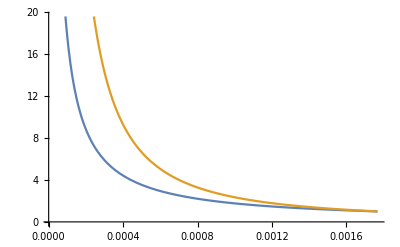

```mathematica
Plot[{0.0017673778507420201/nb,0.0017673778507420201^(3/2)/nb^(3/2)},{nb,0.00001,0.0017673778507420201}]
```

```mathematica
FindRoot[1-MMo2pk[[1,3]][k]0.00011459250315671164,{k,0.03}]
```

InterpolatingFunction::dmval: Input value {-0.230703} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.25335} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.110066} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{k→0.0158322}

```mathematica
.
```

{k→0.112497}

```mathematica
MMo1pk[[1,3]][0.11]0.0017673778507420201
```

1.0255

```mathematica
nbMMo2
```

nb→0.000114593

```mathematica
nbfixCMASSngc
```

nb→0.000214872

```mathematica
nbD1
```

nb→0.00079676

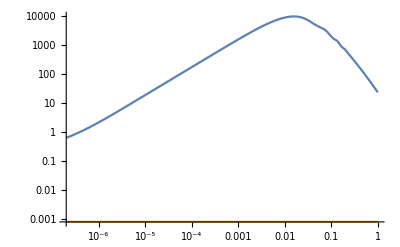

```mathematica
LogLogPlot[{DESI1pk[[1,3]][k],0.0007967599137945827},{k,0.0000002,1}]
```

```mathematica
√2.3//N
```

1.51658

```mathematica
7/5.2
```

1.34615

```mathematica
1.15/0.87
```

1.32184

```mathematica
0.17/0.14
```

1.21429

```mathematica
bfixMMo1
```

{b1→2.64038,b10→0.0582788,b11→0.0484749,b12→0.,b13→0.,b14→0.,b15→0.,b3→-0.509259,b4→0.173747,b6→-0.474809,b7→0.304194,b8→-0.404684,b9→0.0201525,Bc1→7.43532,Bc10→-0.885076,Bc11→-0.119962,Bc12→-0.508033,Bc13→-0.223584,Bc14→-0.266612,Bc2→-2.10226,Bc3→1.78118,Bc4→-0.651552,Bc5→0.143518,Bc6→1.18641,Bc7→-0.620234,Bc8→0.604847,Bc9→-0.565359,c2→1.55869,c4→-0.394199,Tst→13.0719,Bd1→3.73813,Bd2→-0.49911,Bd3→-0.295312,Be1→1.17142,Be2→0.629321,ce2→0.384058,Be3→0.0510186,Be4→-0.0955992,Be5→4.20007,Be6→-0.0645174,Be7→-0.671618,Be8→0.181161,Be9→0.182615,Be10→-0.105637,Be11→0.295589,Be12→-0.299189}

```mathematica
bfixMMo1=Evolve[1,Dg236,changeb1[Evolve[Dg57,1,bfixBOSS],1]];
bfixMMo2=Evolve[1,Dg428,changeb1[Evolve[Dg57,1,bfixBOSS],1]];
```

```mathematica
coeffixMMo1 = Join[bfixMMo1,fnlfix,paramfix,knlMMo1];
coeffixMMo2 = Join[bfixMMo2,fnlfix,paramfix,knlMMo2];
```

```mathematica
coeffixMMo1S1 = Join[{Be1->1},coeffixMMo1];
coeffixMMo2S1 = Join[{Be1->1},coeffixMMo2];
```

Base tab and setting kmax

```mathematica
ktabraw = Table[0.001+i 0.005,{i,1,300}];
```

```mathematica
Basetri  =makeTri[0.02,0.8,0.02];
keffbase = Import["baseTrikeff.mtx"];
```

```mathematica
Bins = Basetri//Flatten//DeleteDuplicates//Sort;
```

```mathematica
Setkmax[kmax_]:=Select[Bins,#<kmax&];
goodTri[kmax_] := Complement[Table[i,{i,1,Length[Basetri]}],Table[Position[Basetri,Complement[Bins,Setkmax[kmax]][[i]]][[All,1]],{i,1,Length[Complement[Bins,Setkmax[kmax]]]}]//Flatten//DeleteDuplicates//Sort];
```

Binning sizes

```mathematica
dkPMM = dk->0.005;
dkBMM=dk->0.02;
```

Powerspectrum kmax

```mathematica
Getσ[ktab_, Cov_]:=Transpose@{ktab,1/(Cov//mono)}//Interpolation;
```

```mathematica
COVCMASSPgen=GetFullzCovP[ktabraw,CMASSpk,CMASSspec,Dg57,bfixBOSS,dkPMM];
COVCMASSPgenNS=GetFullzCovPNS[ktabraw,CMASSpk,CMASSspec,Dg57,bfixBOSSNS,dkPMM];
```

```mathematica
σCMASS = Getσ[ktabraw, COVCMASSPgen];
σCMASSNS = Getσ[ktabraw, COVCMASSPgenNS];
COVMMo1Pkmm=GetFullzCovP[ktabraw,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkPMM];
COVMMo2Pkmm=GetFullzCovP[ktabraw,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkPMM];
COVMMo1PNSkmm=GetFullzCovPNS[ktabraw,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkPMM];
COVMMo2PNSkmm=GetFullzCovPNS[ktabraw,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkPMM];
```

```mathematica
GetSlope[ku_,kd_,pk_]:=(ku+kd)/2(Log[pk[ku]]-Log[pk[kd]])/(ku-kd);
```

```mathematica
GetkmaxNSP[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])2)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
```

```mathematica
GetkmaxNSP2L[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])3)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
GetkmaxNSP1L[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])1)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
```

```mathematica
kmaxMMo1 = GetkmaxNSP[Getσ[ktabraw, COVMMo1PNSkmm],MMo1pk][[1,2]]
kmaxMMo2 =GetkmaxNSP[Getσ[ktabraw, COVMMo2PNSkmm],MMo2pk][[1,2]]
```

0.369008

0.730157

```mathematica
kmaxMMo12L= GetkmaxNSP2L[Getσ[ktabraw, COVMMo1PNSkmm],MMo1pk][[1,2]]
kmaxMMo22L =GetkmaxNSP2L[Getσ[ktabraw, COVMMo2PNSkmm],MMo2pk][[1,2]]
```

0.522474

1.15054

```mathematica
kmaxMMo1Tree = GetkmaxNSP1L[Getσ[ktabraw, COVMMo1PNSkmm],MMo1pk][[1,2]]
kmaxMMo2Tree =GetkmaxNSP1L[Getσ[ktabraw, COVMMo2PNSkmm],MMo2pk][[1,2]]
```

0.173977

0.366747

Get triangles and ktabs

```mathematica
ktabMMo1 = Select[ktabraw,#<kmaxMMo1&];
ktabMMo2 = Select[ktabraw,#<kmaxMMo2&];
```

```mathematica
ktabMMo12L = Select[ktabraw,#<kmaxMMo12L&];
ktabMMo22L = Select[ktabraw,#<1&];
```

```mathematica
keffMMo1 = keffbase[[goodTri[kmaxMMo1]]];
keffMMo2 = keffbase[[goodTri[kmaxMMo2]]];
MMotriangs1 = Basetri[[goodTri[kmaxMMo1]]];
MMotriangs2 = Basetri[[goodTri[kmaxMMo2]]];
```

```mathematica
keffMMo1T = keffbase[[goodTri[kmaxMMo1Tree]]];
keffMMo2T = keffbase[[goodTri[kmaxMMo2Tree]]];
MMotriangs1T = Basetri[[goodTri[kmaxMMo1Tree]]];
MMotriangs2T = Basetri[[goodTri[kmaxMMo2Tree]]];
```

Analytical Covariance with Full redshift

```mathematica
COVMMo1P=GetFullzCovP[ktabMMo1,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkPMM];
COVMMo2P=GetFullzCovP[ktabMMo2,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkPMM];
```

```mathematica
COVMMo1Pn=GetFullzCovPn[ktabMMo1,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkPMM];
COVMMo2Pn=GetFullzCovPn[ktabMMo2,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkPMM];
```

```mathematica
COVMMo1P2L=GetFullzCovP[ktabMMo12L,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkPMM];
COVMMo2P2L=GetFullzCovP[ktabMMo22L,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkPMM];
```

```mathematica
COVMMo1B=GetFullzCovB[MMotriangs1,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkBMM];
COVMMo2B=GetFullzCovB[MMotriangs2,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkBMM];
```

```mathematica
COVMMo1BTree=GetFullzCovB[MMotriangs1T,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkBMM];
COVMMo2BTree=GetFullzCovB[MMotriangs2T,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkBMM];
```

Analytical Covariance with Full redshift- No shot noise

```mathematica
COVMMo1PNS=GetFullzCovPNS[ktabMMo1,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkPMM];
COVMMo2PNS=GetFullzCovPNS[ktabMMo2,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkPMM];
```

```mathematica
COVMMo1PNS2L=GetFullzCovPNS[ktabMMo12L,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkPMM];
COVMMo2PNS2L=GetFullzCovPNS[ktabMMo22L,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkPMM];
```

```mathematica
COVMMo1BNS=GetFullzCovBNS[MMotriangs1,MMo1pk,MMo1spec,Dg236,bfixMMo1,dkBMM];
COVMMo2BNS=GetFullzCovBNS[MMotriangs2,MMo2pk,MMo2spec,Dg428,bfixMMo2,dkBMM];
```

Powerspectrum Derivatives

```mathematica
PMMo1derivs =Monitor[ Table[P1Loopderivs[ktabMMo1[[i]],MMo1pk],{i,1,Length[ktabMMo1]}],i]/.coeffixMMo1/.nbMMo1;
PMMo2derivs = Monitor[Table[P1Loopderivs[ktabMMo2[[i]],MMo2pk],{i,1,Length[ktabMMo2]}],i]/.coeffixMMo2/.nbMMo2;
```

```mathematica
PMMo1derivs2L =Monitor[ Table[P1Loopderivs[ktabMMo12L[[i]],MMo1pk],{i,1,Length[ktabMMo12L]}],i]/.coeffixMMo1/.nbMMo1;
PMMo2derivs2L = Monitor[Table[P1Loopderivs[ktabMMo22L[[i]],MMo2pk],{i,1,Length[ktabMMo22L]}],i]/.coeffixMMo2/.nbMMo2;
```

Bispectrum Derivatives

```mathematica
BMMo1derivsT=Monitor[Table[BTreederivs[keffMMo1T[[si]],MMo1pk]/.Dispatch[coeffixMMo1]/.nbMMo1,{si,1,Length[keffMMo1T]}],si];//AbsoluteTiming
BMMo2derivsT=Monitor[Table[BTreederivs[keffMMo2T[[si]],MMo2pk]/.Dispatch[coeffixMMo2]/.nbMMo2,{si,1,Length[keffMMo2T]}],si];//AbsoluteTiming
```

{8.16597,Null}

{66.4915,Null}

```mathematica
BMMo1derivs=Monitor[Table[B1Loopderivs[keffMMo1[[si]],MMo1pk]/.Dispatch[coeffixMMo1]/.nbMMo1,{si,1,Length[keffMMo1]}],si];//AbsoluteTiming
BMMo2derivs=Monitor[Table[B1Loopderivs[keffMMo2[[si]],MMo2pk]/.Dispatch[coeffixMMo2]/.nbMMo2,{si,1,Length[keffMMo2]}],si];//AbsoluteTiming
```

{1842.65,Null}

{12460.1,Null}

```mathematica
Export["BMMo1derivs.m",BMMo1derivs]
Export["BMMo2derivs.m",BMMo2derivs]
```

BMMo1derivs.m

BMMo2derivs.m

### Fishers

Reduce P-derivatives to monopole and quadrupole

```mathematica
PMMo1monoquad= removelg2[PMMo1derivs]//Expand;
PMMo2monoquad= removelg2[PMMo2derivs]//Expand;
```

Powerspectrum Fishers monoquad

```mathematica
FPMMo1= GetFisherPnew[PMMo1monoquad,COVMMo1P];
FPMMo2 = GetFisherPnew[PMMo2monoquad,COVMMo2P];
```

Bispectrum Fishers - mono

```mathematica
FBMMo1 = GetFisherB[BMMo1derivs,COVMMo1B,Loopmastermono];
FBMMo2 = GetFisherB[BMMo2derivs,COVMMo2B,Loopmastermono];
```

Powerspectrum Fishers full μ

```mathematica
COVMMo1Pnn[n_]=COVMMo1Pn;
COVMMo2Pnn[n_]=COVMMo2Pn;
```

```mathematica
FPMMo1mun[n_]:= GetFisherPnew[PMMo1derivs,COVMMo1Pnn[n]];
FPMMo2mun[n_] := GetFisherPnew[PMMo2derivs,COVMMo2Pnn[n]];
```

```mathematica
ntab = Table[n*0.5,{n,0,10}];
```

```mathematica
MMo1s = Table[FPMMo1mun[ntab[[i]]],{i,1,Length[ntab]}];
MMo2s = Table[FPMMo2mun[ntab[[i]]],{i,1,Length[ntab]}];
```

```mathematica
Table[Allres[MMo1s[[i]]+MMo2s[[i]]]/Allres[MMo1s[[2]]+MMo2s[[2]]],{i,1,Length[ntab]}][[2;;]]//Transpose
```

{{1.,1.22654,1.41012,1.57109,1.71761,1.85402,1.98295,2.10609,2.22462,2.33939},{1.,1.1828,1.33451,1.47056,1.59684,1.71635,1.83088,1.94155,2.04915,2.15424},{1.,1.21286,1.38192,1.52578,1.65264,1.76729,1.87285,1.97142,2.06449,2.15314},{1.,1.16449,1.29835,1.41289,1.51365,1.60401,1.68627,1.76209,1.83268,1.89899},{1.,1.19417,1.33145,1.43917,1.52839,1.60541,1.67415,1.73722,1.79637,1.85279},{1.,1.19417,1.33145,1.43917,1.52839,1.60541,1.67415,1.73722,1.79637,1.85279}}

```mathematica
√ntab[[3;;]]
```

{1.,1.22474,1.41421,1.58114,1.73205,1.87083,2.,2.12132,2.23607}

```mathematica
FPMMo1mu= GetFisherPnew[PMMo1derivs,COVMMo1P];
FPMMo2mu = GetFisherPnew[PMMo2derivs,COVMMo2P];
```

```mathematica
FPMMo1mu2L= GetFisherPnew[PMMo1derivs2L,COVMMo1P2L];
FPMMo2mu2L = GetFisherPnew[PMMo2derivs2L,COVMMo2P2L];
```

Bispectrum Fishers full μ

```mathematica
FBMMo1mu = GetFisherB[BMMo1derivs,COVMMo1B,Loopmaster];
FBMMo2mu = GetFisherB[BMMo2derivs,COVMMo2B,Loopmaster];
```

Bispectrum Fishers full μ Tree

```mathematica
FBMMo1muT = GetFisherB[BMMo1derivsT,COVMMo1BTree,Loopmaster];
FBMMo2muT = GetFisherB[BMMo2derivsT,COVMMo2BTree,Loopmaster];
```

Powerspectrum Fishers full NS

```mathematica
FPMMo1muNS= GetFisherPnew[PMMo1derivs,COVMMo1PNS];
FPMMo2muNS = GetFisherPnew[PMMo2derivs,COVMMo2PNS];
```

Bispectrum Fishers full NS

```mathematica
FBMMo1muNS = GetFisherB[BMMo1derivs,COVMMo1BNS,Loopmaster];
FBMMo2muNS = GetFisherB[BMMo2derivs,COVMMo2BNS,Loopmaster];
```

## MegaMapper - pessimistic

### MMo specifications and derivative computations

MMo numbers fully binned (section 1.2 in arxiv 2209.04322, then arxiv 1903.09208 Table 1 )

```mathematica
(*z,nb,V,N,Dg,fs*)
```

```mathematica
MMpspec = {{2,3,4,5},10^-4{9.8,1.2,1,0.4},10^9{53.47254431,54.28608766,50.11599096,45.09835607},{5.240309342380001*^7,6.5143305192*^6,5.011599096*^6,1.8039342428000001*^6},{0.4218432700320637,0.3202062843007084,0.25772882630869365,0.21561945123476095},{0.9453786646849289,0.9680891481945141,0.9764457658964426,0.9801124389970047}};
```

```mathematica
MMpcut=2;
```

Get zeffs and define cental values

```mathematica
Getzeffs[MMpspec,MMpcut]
```

{2.11057,4.26468}

```mathematica
MMp1spec = MMpspec[[All,;;MMpcut]];
MMp2spec = MMpspec[[All,MMpcut+1;;]];
```

```mathematica
Dg211=0.4076946713668692;
Dg426 =0.24527419781767706;
```

```mathematica
MMp1pk = PlinsubsT[MMp1N,2.11];
MMp2pk = PlinsubsT[MMp2N,4.26];
```

Shotnoise estimates (these are not entering the covariance, so they are not very important)

```mathematica
Getnbeff[MMpspec,MMpcut]
```

{0.000884912,0.0000841192}

```mathematica
nbMMp1 = nb->0.0008849122675164482;
nbMMp2 = nb->0.00008411920987139401;
```

Get knls

```mathematica
Getknl[pk_]:=Quiet[FindRoot[1/(2 π^2)NIntegrate[k^2 pk[k],{k,10^-5,kn}]-1.1525490955287694,{kn,0.5}]]
```

```mathematica
knlMMp1 = {knl->Getknl[MMp1pk[[1,3]]][[1,2]]}
knlMMp2 = {knl->Getknl[MMp2pk[[1,3]]][[1,2]]}
```

{knl→2.66591}

{knl→10.0263}

Parameters bestfit from BOSS, rescaled to MMp. The estimate is  b1 = 1/D(z) (arxiv 1903.09208 Table 1)

```mathematica
bfixMMp1=changeb1[bfixBOSS,1/Dg211];
bfixMMp2=changeb1[bfixBOSS,1/Dg426];
```

```mathematica
coeffixMMp1 = Join[bfixMMp1,fnlfix,paramfix,knlMMp1];
coeffixMMp2 = Join[bfixMMp2,fnlfix,paramfix,knlMMp2];
```

```mathematica
coeffixMMpNS = Join[{Be1->0},coeffixMMp1];
coeffixMMpNS = Join[{Be1->0},coeffixMMp2];
```

Base tab and setting kmax

```mathematica
ktabraw = Table[0.001+i 0.005,{i,1,300}];
```

```mathematica
Basetri  =makeTri[0.02,0.8,0.02];
keffbase = Import["baseTrikeff.mtx"];
```

```mathematica
Bins = Basetri//Flatten//DeleteDuplicates//Sort;
```

```mathematica
Setkmax[kmax_]:=Select[Bins,#<kmax&];
goodTri[kmax_] := Complement[Table[i,{i,1,Length[Basetri]}],Table[Position[Basetri,Complement[Bins,Setkmax[kmax]][[i]]][[All,1]],{i,1,Length[Complement[Bins,Setkmax[kmax]]]}]//Flatten//DeleteDuplicates//Sort];
```

Binning sizes

```mathematica
dkPMM = dk->0.005;
dkBMM=dk->0.02;
```

Powerspectrum kmax

```mathematica
Getσ[ktab_, Cov_]:=Transpose@{ktab,1/(Cov//mono)}//Interpolation;
```

```mathematica
COVCMASSPgen=GetFullzCovP[ktabraw,CMASSpk,CMASSspec,Dg57,bfixBOSS,dkPMM];
COVCMASSPgenNS=GetFullzCovPNS[ktabraw,CMASSpk,CMASSspec,Dg57,bfixBOSSNS,dkPMM];
```

```mathematica
σCMASS = Getσ[ktabraw, COVCMASSPgen];
σCMASSNS = Getσ[ktabraw, COVCMASSPgenNS];
COVMMp1Pkmm=GetFullzCovP[ktabraw,MMp1pk,MMp1spec,Dg211,bfixMMp1,dkPMM];
COVMMp2Pkmm=GetFullzCovP[ktabraw,MMp2pk,MMp2spec,Dg426,bfixMMp2,dkPMM];
COVMMp1PNSkmm=GetFullzCovPNS[ktabraw,MMp1pk,MMp1spec,Dg211,bfixMMp1,dkPMM];
COVMMp2PNSkmm=GetFullzCovPNS[ktabraw,MMp2pk,MMp2spec,Dg426,bfixMMp2,dkPMM];
```

```mathematica
GetSlope[ku_,kd_,pk_]:=(ku+kd)/2(Log[pk[ku]]-Log[pk[kd]])/(ku-kd);
```

```mathematica
GetkmaxNSP[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])2)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
```

```mathematica
GetkmaxNSP2L[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])3)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
GetkmaxNSP1L[σ1_,pk1_]:=Quiet[FindRoot[√(σ1[kmm]/σCMASSNS[0.22])-(pk1[[1,3]][kmm])/(CMASSpk[[1,3]][0.22])(kmm/(Getknl[pk1[[1,3]]][[1,2]]))^((3+GetSlope[0.8kmm,1.2kmm,CMASSpk[[1,3]]])1)(0.22/0.7)^(-(3+(-1.8))2),{kmm,0.1}]]
```

```mathematica
Getσ[ktabraw, COVMMp1PNSkmm]
```

InterpolatingFunction[…]

```mathematica
kmaxMMp1 = GetkmaxNSP[Getσ[ktabraw, COVMMp1PNSkmm],MMp1pk][[1,2]]
kmaxMMp2 =GetkmaxNSP[Getσ[ktabraw, COVMMp2PNSkmm],MMp2pk][[1,2]]
```

0.317393

0.698532

```mathematica
kmaxMMp12L= GetkmaxNSP2L[Getσ[ktabraw, COVMMp1PNSkmm],MMp1pk][[1,2]]
kmaxMMp22L =GetkmaxNSP2L[Getσ[ktabraw, COVMMp2PNSkmm],MMp2pk][[1,2]]
```

0.468859

1.09056

```mathematica
kmaxMMp1Tree = GetkmaxNSP1L[Getσ[ktabraw, COVMMp1PNSkmm],MMp1pk][[1,2]]
kmaxMMp2Tree =GetkmaxNSP1L[Getσ[ktabraw, COVMMp2PNSkmm],MMp2pk][[1,2]]
```

0.163353

0.327084

Get triangles and ktabs

```mathematica
ktabMMp1 = Select[ktabraw,#<kmaxMMp1&];
ktabMMp2 = Select[ktabraw,#<kmaxMMp2&];
```

```mathematica
keffMMp1 = keffbase[[goodTri[kmaxMMp1]]];
keffMMp2 = keffbase[[goodTri[kmaxMMp2]]];
MMptriangs1 = Basetri[[goodTri[kmaxMMp1]]];
MMptriangs2 = Basetri[[goodTri[kmaxMMp2]]];
```

```mathematica
keffMMp1T = keffbase[[goodTri[kmaxMMp1Tree]]];
keffMMp2T = keffbase[[goodTri[kmaxMMp2Tree]]];
MMptriangs1T = Basetri[[goodTri[kmaxMMp1Tree]]];
MMptriangs2T = Basetri[[goodTri[kmaxMMp2Tree]]];
```

Analytical Covariance with Full redshift

```mathematica
COVMMp1P=GetFullzCovP[ktabMMp1,MMp1pk,MMp1spec,Dg211,bfixMMp1,dkPMM];
COVMMp2P=GetFullzCovP[ktabMMp2,MMp2pk,MMp2spec,Dg426,bfixMMp2,dkPMM];
```

```mathematica
COVMMp1B=GetFullzCovB[MMptriangs1,MMp1pk,MMp1spec,Dg211,bfixMMp1,dkBMM];
COVMMp2B=GetFullzCovB[MMptriangs2,MMp2pk,MMp2spec,Dg426,bfixMMp2,dkBMM];
```

```mathematica
COVMMp1BTree=GetFullzCovB[MMptriangs1T,MMp1pk,MMp1spec,Dg211,bfixMMp1,dkBMM];
COVMMp2BTree=GetFullzCovB[MMptriangs2T,MMp2pk,MMp2spec,Dg426,bfixMMp2,dkBMM];
```

Analytical Covariance with Full redshift- No shot noise

```mathematica
COVMMp1PNS=GetFullzCovPNS[ktabMMp1,MMp1pk,MMp1spec,Dg211,bfixMMp1,dkPMM];
COVMMp2PNS=GetFullzCovPNS[ktabMMp2,MMp2pk,MMp2spec,Dg426,bfixMMp2,dkPMM];
```

```mathematica
COVMMp1BNS=GetFullzCovBNS[MMptriangs1,MMp1pk,MMp1spec,Dg211,bfixMMp1,dkBMM];
COVMMp2BNS=GetFullzCovBNS[MMptriangs2,MMp2pk,MMp2spec,Dg426,bfixMMp2,dkBMM];
```

Powerspectrum Derivatives

```mathematica
PMMp1derivs =Monitor[ Table[P1Loopderivs[ktabMMp1[[i]],MMp1pk],{i,1,Length[ktabMMp1]}],i]/.coeffixMMp1/.nbMMp1;
PMMp2derivs = Monitor[Table[P1Loopderivs[ktabMMp2[[i]],MMp2pk],{i,1,Length[ktabMMp2]}],i]/.coeffixMMp2/.nbMMp2;
```

Bispectrum Derivatives

```mathematica
BMMp1derivsT=Monitor[Table[BTreederivs[keffMMp1T[[si]],MMp1pk]/.Dispatch[coeffixMMp1]/.nbMMp1,{si,1,Length[keffMMp1T]}],si];//AbsoluteTiming
BMMp2derivsT=Monitor[Table[BTreederivs[keffMMp2T[[si]],MMp2pk]/.Dispatch[coeffixMMp2]/.nbMMp2,{si,1,Length[keffMMp2T]}],si];//AbsoluteTiming
```

{8.371,Null}

{51.0997,Null}

```mathematica
BMMp1derivs=Monitor[Table[B1Loopderivs[keffMMp1[[si]],MMp1pk]/.Dispatch[coeffixMMp1]/.nbMMp1,{si,1,Length[keffMMp1]}],si];//AbsoluteTiming
BMMp2derivs=Monitor[Table[B1Loopderivs[keffMMp2[[si]],MMp2pk]/.Dispatch[coeffixMMp2]/.nbMMp2,{si,1,Length[keffMMp2]}],si];//AbsoluteTiming
```

{1142.21,Null}

{11187.1,Null}

### Fishers

Reduce P-derivatives to monopole and quadrupole

```mathematica
PMMp1monoquad= removelg2[PMMp1derivs]//Expand;
PMMp2monoquad= removelg2[PMMp2derivs]//Expand;
```

Powerspectrum Fishers monoquad

```mathematica
FPMMp1= GetFisherPnew[PMMp1monoquad,COVMMp1P];
FPMMp2 = GetFisherPnew[PMMp2monoquad,COVMMp2P];
```

Bispectrum Fishers - mono

```mathematica
FBMMp1 = GetFisherB[BMMp1derivs,COVMMp1B,Loopmastermono];
FBMMp2 = GetFisherB[BMMp2derivs,COVMMp2B,Loopmastermono];
```

Powerspectrum Fishers full μ

```mathematica
FPMMp1mu= GetFisherPnew[PMMp1derivs,COVMMp1P];
FPMMp2mu = GetFisherPnew[PMMp2derivs,COVMMp2P];
```

Bispectrum Fishers full μ

```mathematica
FBMMp1mu = GetFisherB[BMMp1derivs,COVMMp1B,Loopmaster];
FBMMp2mu = GetFisherB[BMMp2derivs,COVMMp2B,Loopmaster];
```

Bispectrum Fishers full μ Tree

```mathematica
FBMMp1muT = GetFisherB[BMMp1derivsT,COVMMp1BTree,Loopmaster];
FBMMp2muT = GetFisherB[BMMp2derivsT,COVMMp2BTree,Loopmaster];
```

Powerspectrum Fishers full NS

```mathematica
FPMMp1muNS= GetFisherPnew[PMMp1derivs,COVMMp1PNS];
FPMMp2muNS = GetFisherPnew[PMMp2derivs,COVMMp2PNS];
```

Bispectrum Fishers full NS

```mathematica
FBMMp1muNS = GetFisherB[BMMp1derivs,COVMMp1BNS,Loopmaster];
FBMMp2muNS = GetFisherB[BMMp2derivs,COVMMp2BNS,Loopmaster];
```

## Double check things

```mathematica
cosmobias = DeleteCases[Join[{Ωm,h,lnAs,ωb},BAllcoefs],b12|b13|b14|b15];
cosmobiasns = DeleteCases[Join[{Ωm,h,lnAs,ns,ωb},BAllcoefs],b12|b13|b14|b15];
fnlbiasloc = DeleteCases[Join[{fNLloc},BAllcoefs],b12|b13|b14|b15];
fnlbiaseq = DeleteCases[Join[{fNLeq},BAllcoefs],b12|b13|b14|b15];
fnlbiasorth = DeleteCases[Join[{fNLorth},BAllcoefs],b12|b13|b14|b15];
fnlbias = DeleteCases[Join[fnlcoefs[[2;;]],BAllcoefs],b12|b13|b14|b15];
```

```mathematica
Cosmores[Fisher_]:=GetError[SubFisher[Fisher+Priors,cosmobias]][[;;3]];
Cosmoresns[Fisher_]:=GetError[SubFisher[Fisher+Priors,cosmobiasns]][[;;4]];
Locres[Fisher_]:=GetError[SubFisher[Fisher+Priors,fnlbiasloc]][[1]]
Eqres[Fisher_]:=GetError[SubFisher[Fisher+Priors,fnlbiaseq]][[1]]
Orthres[Fisher_]:=GetError[SubFisher[Fisher+Priors,fnlbiasorth]][[1]]
FNLres[Fisher_]:={Locres[Fisher],Eqres[Fisher],Orthres[Fisher]}
```

```mathematica
cosmobias2 = DeleteCases[Join[{ωb,lnAs,ns,h,Ωm,mν},BAllcoefs],b12|b13|b14|b15];
```

```mathematica
Cosmores2[Fisher_]:=GetError[SubFisher[Fisher+Priors,cosmobias2]][[2;;8]];
Cosmores3[Fisher_]:=(GetError[SubFisher[Fisher+Priors,cosmobias2]][[2;;8]])/(GetError[SubFisher[Fisher+Priors,cosmobias2]][[2]]);
```

```mathematica
Allres[Fisher_]:={Cosmores[Fisher],FNLres[Fisher]}//Flatten;Allresns[Fisher_]:={Cosmoresns[Fisher],FNLres[Fisher]}//Flatten;
```

```mathematica
Cosmores[FPMMo1mu+FPMMo2mu]/Cosmores[FPMMo1mu2L+FPMMo2mu2L]

Cosmores[FPMMo1muNS+FPMMo2muNS]/Cosmores[FPMMo1muNS2L+FPMMo2muNS2L]
```

{1.10388,1.04496,1.13115}

{2.74438,1.41199,1.23584}

```mathematica
Cosmores[FPCnewmubase+FPLnewmubase]
Cosmores[FPCnewmu2L+FPLnewmu2L]
Cosmores[FPCnewmubaseNS+FPLnewmubaseNS]
Cosmores[FPCnewmu2LNS+FPLnewmu2LNS]
```

{0.00999048,0.0116709,0.136032}

{0.00853196,0.0106383,0.119929}

{0.00589695,0.00670218,0.0901101}

{0.00476274,0.00552661,0.072664}

```mathematica
Cosmores[FPCnewmubase+FPLnewmubase]/Cosmores[FPCnewmu2L+FPLnewmu2L]
```

{1.17095,1.09707,1.13428}

```mathematica
Cosmores[FPCnewmubaseNS+FPLnewmubaseNS]/Cosmores[FPCnewmu2LNS+FPLnewmu2LNS]
```

{1.23814,1.21271,1.24009}

```mathematica
Allres[FPD1+FPD2+FBD1+FBD2]
```

{0.00168465+0. ⅈ,0.00217135+0. ⅈ,0.0248529+0. ⅈ,16.7873+0. ⅈ,157.222+0. ⅈ,46.6134+0. ⅈ}

```mathematica
Allres[FPD12+FPD22+FBD1+FBD2]
```

{0.00165444+0. ⅈ,0.00214852+0. ⅈ,0.0242853+0. ⅈ,4.08004+0. ⅈ,156.95+0. ⅈ,46.5664+0. ⅈ}

```mathematica
FNLres[Exporter[FPMMp1+FPMMp2,"Fishers3/MMp/Panafullz.mtx"]
Exporter[FPMMp1+FPMMp2+FBMMp1+FBMMp2,"Fishers3/MMp/PBanafullz.mtx"]]
```

```mathematica
FNLres[Re[FPMMp1+FPMMp2+FBMMp1+FBMMp2]]
```

{3.2147,68.6089,22.0078}

```mathematica
Allparams
```

```mathematica
{fNLorth,b1,c2,b3,b4,c4,b6,b7,b8,b9,b10,b11,Bc1,Bc2,Bc3,Bc4,Be1,Be2,ce2,Bc5,Bc6,Bc7,Bc8,Bc9,Bc10,Bc11,Bc12,Bc13,Bc14,Bd1,Bd2,Bd3,Be3,Be4,Be5,Be6,Be7,Be8,Be9,Be10,Be11,Be12,Tst}//Dimensions
```

{43}

```mathematica
Allparams//Dimensions
```

{51}

```mathematica
Re[FPMMp1+FPMMp2+FBMMp1+FBMMp2]//Dimensions
```

{55,55}

```mathematica
Allres[Re[FPMMp1mu+FPMMp2mu+FBMMp1mu+FBMMp2mu]]
Allres[Re[FPMMp1+FPMMp2]]
```

{0.000591786,0.0008861,0.00701766,2.70041,65.4392,19.3403}

{0.00181292,0.00246668,0.0195497,4.85857,881.68,881.68}

```mathematica
(√((GetFExp[Re[FPMMp1+FPMMp2+FBMMp1+FBMMp2]][[9;;,9;;]])//Inverse//Diagonal))[[1]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0376947,-220.268,-3.86333,-2.46395,0.418167,0.271839,-5.40248,0.166413,-7.48932,11.5512,«33»},«9»,«33»} may contain significant numerical errors.

22.0078

```mathematica
Cosmores[PFisherCMASSngcAnafit+BFisherCMASSngcAnafit]
```

{0.00998031,0.012503,0.137997}

```mathematica
Allres[PFisherCMASSngcAnafit+PFisherCMASSsgcAnafit+PFisherLOWZngcAnafit+PFisherLOWZsgcAnafit+BFisherCMASSngcAnafit+BFisherCMASSsgcAnafit+BFisherLOWZngcAnafit+BFisherLOWZsgcAnafit]
```

{0.00628221,0.00730036,0.0751452,36.6901,378.294,105.904}

```mathematica
Allres[PFisherCMASSngcmu+PFisherCMASSsgcmu+PFisherLOWZngcmu+PFisherLOWZsgcmu+BFisherCMASSngcmu+BFisherCMASSsgcmu+BFisherLOWZngcmu+BFisherLOWZsgcmu]
```

{0.0057946,0.00706915,0.0614422,33.2175,357.124,102.734}

```mathematica
Allres[Re[FPD1+FPD2]]
```

{0.0045611,0.00535649,0.0418218,41.1279,15663.5,15663.5}

```mathematica
Allres[Re[FPMMo1+FPMMo2]]
```

{0.00142652,0.00191718,0.0172423,3.99738,795.446,795.446}

```mathematica
Re[FPMMo1mu+FPMMo2mu+FBMMo1mu+FBMMo2mu]
```

```mathematica
Allres[Re[FPMMo1mu+FPMMo2mu+FBMMo1mu+FBMMo2mu]]
```

{0.000519458,0.000774428,0.00607499,1.76635,45.2808,12.5207}

```mathematica
Allres[Re[FPMMp1+FPMMp2]]
Allres[Re[FPMMp1+FPMMp2+FBMMp11+FBMMp21]]
```

{0.00181292,0.00246668,0.0195497,4.85857,881.68,881.68}

{0.000603585,0.000872551,0.0125454,2.7582,30.8285,9.34331}

```mathematica
Allresns[Re[FPMMp1+FPMMp2]]
Allresns[Re[FPMMp1+FPMMp2+FBMMp11+FBMMp21]]
```

{0.00439102,0.00351543,0.0272569,0.245109,4.85857,881.68,881.68}

{0.00149688,0.00122547,0.0137186,0.0873162,2.7582,30.8285,9.34331}

```mathematica
Allres[Re[FPMMo1+FPMMo2]]
Allres[Re[FPMMo1+FPMMo2+FBMMo1+FBMMo2]]
```

{0.00142652,0.00191718,0.0172423,3.99738,795.446,795.446}

{0.00054595,0.000798468,0.0101419,2.1231,48.1187,14.3831}

```mathematica
Allresns[Re[FPMMo1+FPMMo2]]
Allresns[Re[FPMMo1+FPMMo2+FBMMo1+FBMMo2]]
```

{0.0035845,0.00284057,0.0239717,0.200648,3.99738,795.446,795.446}

{0.00130816,0.00109376,0.0114831,0.0748866,2.1231,48.1187,14.3831}

```mathematica
Allresns[Re[FPD1mu+FPD2mu+FBD1+FBD2]]
```

{0.00381276,0.00316745,0.0328807,0.24081,17.7213,149.375,48.4427}

```mathematica
Allresns[Re[FPD1mu2L+FPD2mu2L+FBD1+FBD2]]
```

{0.00366874,0.00307313,0.0271805,0.212787,16.4676,140.813,47.4168}

```mathematica
Allresns[Re[FPD1mu2L+FPD2mu2L]]
Allresns[Re[FPD1mu+FPD2mu]]
```

{0.00697854,0.00582831,0.0360368,0.375298,34.0331,7604.53,7604.53}

{0.00750167,0.00642709,0.0522887,0.45142,40.781,13553.5,13553.5}

```mathematica
FNLres[FPD1mu2L+FPD2mu2L]
```

{34.0331,7604.53,7604.53}

```mathematica
Allres[Re[FPD1+FPD2+FBD1+FBD2]]
```

{0.00219507,0.00269841,0.029716,17.731,149.733,49.0424}

```mathematica
Allresns[Re[FPD1+FPD2+FBD1+FBD2]]
```

{0.00383806,0.00317018,0.0325032,0.243377,17.731,149.733,49.0424}

```mathematica
0.07488662781852515*mνback
```

0.022466

```mathematica
Allresns[PFisherCMASSngcmu+PFisherCMASSsgcmu+PFisherLOWZngcmu+PFisherLOWZsgcmu+0(BFisherCMASSngcmu+BFisherCMASSsgcmu+BFisherLOWZngcmu+BFisherLOWZsgcmu)]
```

{0.0128776,0.0118708,0.122661,0.722381,45.9352,32110.5,32110.5}

```mathematica
0.7223805522190746*mνback
```

0.216714

```mathematica
1-nsback
```

0.035

```mathematica
Allres[Re[FBMMo12+FBMMo22]]
```

{0.000457277,0.000659486,0.016623,2.76654,60.887,18.1195}

```mathematica
Chop[Im[FBMMo2mu],10^-3]//Flatten//DeleteDuplicates
```

{0}

```mathematica
FPMMo1mu+FPMMo2mu+FBMMo1mu+FBMMo2mu
```

{{2.32084×10^7-0.00130162 ⅈ,1.75715×10^7+0.000879333 ⅈ,1.29941×10^8-0.00415581 ⅈ,8.85525×10^7-0.000563706 ⅈ,47,-26781.7+0.0000160131 ⅈ,-130115.+0.0000255855 ⅈ,85739.3-0.000025802 ⅈ,0.+0. ⅈ},53,{0.+0. ⅈ,53,1}}
 |  |  |  |

```mathematica
.
```

{0.00459745,0.00552865,0.043055,41.1888,12548.5,12548.5}

```mathematica
Allres[Re[FPD1mu+FPD2mu+FBD1mu+FBD2mu]]
```

{0.00213315,0.0027053,0.0220452,14.1088,135.546,44.0601}

```mathematica
.
```

{0.00273209,0.00345606,0.0267393,13.6108,129.848,42.6003}

```mathematica
Cosmores[CMASSNGCFisherFullPB+CMASSSGCFisherFullPB+LOWZNGCFisherFullPB+LOWZSGCFisherFullPB]
```

{0.00696407,0.0086251,0.0888636}

```mathematica
Import["Fishers/P4skyanafit.mtx"]//Dimensions
```

{177,177}

```mathematica
AllParams
```

{lnAs,ns,h,Ωm,ωb,mν,fNLloc,fNLeq,fNLorth,b1,c2,b3,b4,c4,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,Bc1,Bc2,Bc3,Bc4,Be1,Be2,ce2,Bc5,Bc6,Bc7,Bc8,Bc9,Bc10,Bc11,Bc12,Bc13,Bc14,Bd1,Bd2,Bd3,Be3,Be4,Be5,Be6,Be7,Be8,Be9,Be10,Be11,Be12,Tst}

```mathematica
Allparams = DeleteCases[AllParams,b12|b13|b14|b15];
```

```mathematica
GetFExp[Fisher_]:=SubFisher[Fisher+Priors,Allparams]
GetFExp4[Fisher_]:=SubFisher4sky[Fisher+Prior4sky,Allparams]
```

```mathematica
Exporter[Fisher_,name_]:=Export[name,GetFExp[Fisher]]
Exporter4[Fisher_,name_]:=Export[name,GetFExp4[Fisher]]
```

```mathematica
Exporter4[CombineMs[{PFisherCMASSngcAnafit,PFisherCMASSsgcAnafit,PFisherLOWZngcAnafit,PFisherLOWZsgcAnafit}],"Fishers/P4skyAnafitv2.mtx"]
Exporter4[CombineMs[{PFisherCMASSngcAnafit+BFisherCMASSngcAnafit,PFisherCMASSsgcAnafit+BFisherCMASSsgcAnafit,PFisherLOWZngcAnafit+BFisherLOWZngcAnafit,PFisherLOWZsgcAnafit+BFisherLOWZsgcAnafit}],"Fishers/PB4skyAnafitv2.mtx"]
```

Fishers/P4skyAnafitv2.mtx

Fishers/PB4skyAnafitv2.mtx

## Exports

```mathematica
Allparams = DeleteCases[AllParams,b12|b13|b14|b15];
```

```mathematica
GetFExp[Fisher_]:=SubFisher[Fisher+Priors,Allparams]
GetFExp4[Fisher_]:=SubFisher4sky[Fisher+Prior4sky,Allparams]
```

```mathematica
Exporter[Fisher_,name_]:=Export[name,GetFExp[Fisher]]
Exporter4[Fisher_,name_]:=Export[name,GetFExp4[Fisher]]
```

```mathematica
Be1/.bfixMMo1
```

1.17142

### BOSS Exports

Full P results w/o 4 sky correlation

```mathematica
Exporter4[CombineMs[{CMASSNGCFisherFullP,CMASSSGCFisherFullP,LOWZNGCFisherFullP,LOWZSGCFisherFullP}],"Fishers2/BOSS/Pfull4sky.mtx"]
Exporter[CMASSNGCFisherFullP+CMASSSGCFisherFullP+LOWZNGCFisherFullP+LOWZSGCFisherFullP,"Fishers2/BOSS/Pfullnoskycorr.mtx"]
```

Fishers2/BOSS/Pfull4sky.mtx

Fishers2/BOSS/Pfullnoskycorr.mtx

Full PB cross w/o 4 sky correlation

```mathematica
Exporter4[CombineMs[{CMASSNGCFisherFullPB,CMASSSGCFisherFullPB,LOWZNGCFisherFullPB,LOWZSGCFisherFullPB}],"Fishers2/BOSS/PBcross4sky.mtx"]
Exporter[CMASSNGCFisherFullPB+CMASSSGCFisherFullPB+LOWZNGCFisherFullPB+LOWZSGCFisherFullPB,"Fishers2/BOSS/PBcrossnoskycorr.mtx"]
```

Fishers2/BOSS/PBcross4sky.mtx

Fishers2/BOSS/PBcrossnoskycorr.mtx

Numerical covariance Diagonals  w/o 4 sky correlation,  w/o B

```mathematica
Exporter4[CombineMs[{PFisherCMASSngcNumD,PFisherCMASSsgcNumD,PFisherLOWZngcNumD,PFisherLOWZsgcNumD}],"Fishers2/BOSS/PNumD4sky.mtx"]
Exporter[PFisherCMASSngcNumD+PFisherCMASSsgcNumD+PFisherLOWZngcNumD+PFisherLOWZsgcNumD,"Fishers2/BOSS/PNumDnoskycorr.mtx"]
```

Fishers2/BOSS/PNumD4sky.mtx

Fishers2/BOSS/PNumDnoskycorr.mtx

```mathematica
Exporter4[CombineMs[{PFisherCMASSngcNumD+BFisherCMASSngcNumD,PFisherCMASSsgcNumD+BFisherCMASSsgcNumD,PFisherLOWZngcNumD+BFisherLOWZngcNumD,PFisherLOWZsgcNumD+BFisherLOWZsgcNumD}],"Fishers2/BOSS/PBNumD4sky.mtx"]
Exporter[PFisherCMASSngcNumD+BFisherCMASSngcNumD+PFisherCMASSsgcNumD+BFisherCMASSsgcNumD+PFisherLOWZngcNumD+BFisherLOWZngcNumD+PFisherLOWZsgcNumD+BFisherLOWZsgcNumD,"Fishers2/BOSS/PBNumDnoskycorr.mtx"]
```

Fishers2/BOSS/PBNumD4sky.mtx

Fishers2/BOSS/PBNumDnoskycorr.mtx

Analytical covariance with full redshift dependence,  w/o B

```mathematica
Exporter[FPCnew+FPLnew,"Fishers2/BOSS/Panafullz.mtx"]
Exporter[FPCnew+FPLnew+FBCnew+FBLnew,"Fishers2/BOSS/PBanafullz.mtx"]
```

Fishers2/BOSS/Panafullz.mtx

Fishers2/BOSS/PBanafullz.mtx

Analytical covariance with full redshift dependence,  w/o B no shot noise (full mu)

```mathematica
Exporter[FPCnewNS+FPLnewNS,"Fishers2/BOSS/PanamufullzNS.mtx"]
Exporter[FPCnewNS+FPLnewNS+FBCnewNS+FBLnewNS,"Fishers2/BOSS/PBanamufullzNS.mtx"]
```

Fishers2/BOSS/PanamufullzNS.mtx

Fishers2/BOSS/PBanamufullzNS.mtx

Analytical covariance with full redshift dependence full mu dependence,  w/o B

```mathematica
Exporter[FPCnewmu+FPLnewmu,"Fishers2/BOSS/Panamufullz.mtx"]
Exporter[FPCnewmu+FPLnewmu+FBCnewmu+FBLnewmu,"Fishers2/BOSS/PBanamufullz.mtx"]
```

Fishers2/BOSS/Panamufullz.mtx

Fishers2/BOSS/PBanamufullz.mtx

### DESI Exports

Analytical covariance with full redshift dependence,  w/o B

```mathematica
Exporter[FPD1+FPD2,"Fishers2/DESI/Panafullz.mtx"]
Exporter[FPD1+FPD2+FBD1+FBD2,"Fishers2/DESI/PBanafullz.mtx"]
```

Fishers2/DESI/Panafullz.mtx

Fishers2/DESI/PBanafullz.mtx

Analytical covariance with full redshift dependence, all multipoles,  w/o B

```mathematica
Exporter[FPD1mu+FPD2mu,"Fishers2/DESI/Panamufullz.mtx"]
Exporter[FPD1mu+FPD2mu+FBD1mu+FBD2mu,"Fishers2/DESI/PBanamufullz.mtx"]
```

Fishers2/DESI/Panamufullz.mtx

Fishers2/DESI/PBanamufullz.mtx

Analytical covariance with full redshift dependence, all multipoles, 2loop,  w/o B

```mathematica
Exporter[FPD1mu2L+FPD2mu2L,"Fishers2/DESI/Panamufullz2L.mtx"]
Exporter[FPD1mu2L+FPD2mu2L+FBD1mu+FBD2mu,"Fishers2/DESI/PBanamufullz2L.mtx"]
```

Fishers2/DESI/Panamufullz2L.mtx

Fishers2/DESI/PBanamufullz2L.mtx

Analytical covariance with full redshift dependence, all multipoles, Tree B w/o B

```mathematica
Exporter[FPD1mu+FPD2mu+FBD1muT+FBD2muT,"Fishers2/DESI/PBanamufullzT.mtx"]
```

Fishers2/DESI/PBanamufullzT.mtx

Analytical covariance with full redshift dependence, all multipoles, NS,  w/o B

```mathematica
Exporter[FPD1muNS+FPD2muNS,"Fishers2/DESI/PanamufullzNS.mtx"]
Exporter[FPD1muNS+FPD2muNS+FBD1muNS+FBD2muNS,"Fishers2/DESI/PBanamufullzNS.mtx"]
```

Fishers2/DESI/PanamufullzNS.mtx

Fishers2/DESI/PBanamufullzNS.mtx

### MegaMapper optimistic Exports

Analytical covariance with full redshift dependence,  w/o B

```mathematica
Exporter[FPMMo1+FPMMo2,"Fishers2/MMo/Panafullz.mtx"]
Exporter[FPMMo1+FPMMo2+FBMMo1+FBMMo2,"Fishers2/MMo/PBanafullz.mtx"]
```

Fishers2/MMo/Panafullz.mtx

Fishers2/MMo/PBanafullz.mtx

Analytical covariance with full redshift dependence, all multipoles,  w/o B

```mathematica
Exporter[FPMMo1mu+FPMMo2mu,"Fishers2/MMo/Panamufullz.mtx"]
Exporter[FPMMo1mu+FPMMo2mu+FBMMo1mu+FBMMo2mu,"Fishers2/MMo/PBanamufullz.mtx"]
```

Fishers2/MMo/Panamufullz.mtx

Fishers2/MMo/PBanamufullz.mtx

Analytical covariance with full redshift dependence, all multipoles, Tree B w/o B

```mathematica
Exporter[FPMMo1mu+FPMMo2mu+FBMMo1muT+FBMMo2muT,"Fishers2/MMo/PBanamufullzT.mtx"]
```

Fishers2/MMo/PBanamufullzT.mtx

Analytical covariance with full redshift dependence, all multipoles,  NS w/o B

```mathematica
Exporter[FPMMo1muNS+FPMMo2muNS,"Fishers2/MMo/PanamufullzNS.mtx"]
Exporter[FPMMo1muNS+FPMMo2muNS+FBMMo1muNS+FBMMo2muNS,"Fishers2/MMo/PBanamufullzNS.mtx"]
```

Fishers2/MMo/PanamufullzNS.mtx

Fishers2/MMo/PBanamufullzNS.mtx

### MegaMapper pesimistic Exports

Analytical covariance with full redshift dependence,  w/o B

```mathematica
Exporter[FPMMp1+FPMMp2,"Fishers/MMp/Panafullz.mtx"]
Exporter[FPMMp1+FPMMp2+FBMMp1+FBMMp2,"Fishers/MMp/PBanafullz.mtx"]
```

Fishers/MMp/Panafullz.mtx

Fishers/MMp/PBanafullz.mtx

Analytical covariance with full redshift dependence, all multipoles,  w/o B

```mathematica
Exporter[FPMMp1mu+FPMMp2mu,"Fishers/MMp/Panamufullz.mtx"]
Exporter[FPMMp1mu+FPMMp2mu+FBMMp1mu+FBMMp2mu,"Fishers/MMp/PBanamufullz.mtx"]
```

Fishers/MMp/Panamufullz.mtx

Fishers/MMp/PBanamufullz.mtx

Analytical covariance with full redshift dependence, all multipoles, Tree B w/o B

```mathematica
Exporter[FPMMp1mu+FPMMp2mu+FBMMp1muT+FBMMp2muT,"Fishers/MMp/PBanamufullzT.mtx"]
```

Fishers/MMp/PBanamufullzT.mtx

Analytical covariance with full redshift dependence, all multipoles,  NS w/o B

```mathematica
Exporter[FPMMp1muNS+FPMMp2muNS,"Fishers/MMp/PanamufullzNS.mtx"]
Exporter[FPMMp1muNS+FPMMp2muNS+FBMMp1muNS+FBMMp2muNS,"Fishers/MMp/PBanamufullzNS.mtx"]
```

Fishers/MMp/PanamufullzNS.mtx

Fishers/MMp/PBanamufullzNS.mtx